```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

## Load and preprocessing

### Scanning Parameters

#### masses

```mathematica
mpDPoints = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-1,3}];(*We will scan from 10^-1 GeV to a TeV in increments of 10*) 
mpDPointshigh = mpDPoints[[4;;]];
mpDPointslow = Table["mpD"->10^i 10^9("JpereV")/("c")^2/.SIConstRepl,{i,-3,-2}];(*1 MeV is lowest mass given constraints on ϵ and the fact that we are scanning over meD <= 10^-2 mpD. So at 10 MeV,we run into the red giant cooling bound (since the mass of the lightest species must be above 0.1 MeV)*)


mpDPointshigher = Table["mpD"->10^i 10^12("JpereV")/("c")^2/.SIConstRepl,{i,1,3}];

mpDPointslower = Table["mpD"->10^i 10^6("JpereV")/("c")^2/.SIConstRepl,{i,-2,-1}]; 
(*These values of mpD are ruled out for by stellar cooling bounds, but are the lowest valued meD can be that is consistent with them, hence these values will be used to show capture and evaporation rates for the dark electrons *)
```

```mathematica
meDPoints = Table["meD/mpD"->10^i,{i,-4,-2,2}];(*For each value of mpD we will scan over meD/mpD of 10^-4 and 10^-2*)
```

#### v0

```mathematica
v0Points = {20,220}10^3 ;(*[ms^-1] - average velocity of local aDM for Halo and Disk cases*)
```

#### fD

```mathematica
fDpoints = Table[10^i,{i,-3,-1}];
```

#### κ

```mathematica
κpoints = Table[10^i,{i,-14,-7}];
```

```mathematica
mpDPointslow
```

{mpD→1.78×10^-29}

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

### For Δr

#### Read EL dicts

Nuclear

```mathematica
FeNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/FeNuc0ELOutputDict"];
MgNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/MgNuc0ELOutputDict"];
SiNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/SiNuc0ELOutputDict"];
ONuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/ONuc0ELOutputDict"];
```

Electronic

```mathematica
FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];
```

### Electronic dσ/dE_R Interpolation Tables

#### 0.1 GeV

```mathematica
FeσDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],FeTotalparams[[i]],10,60,10^-4,4,True,True],{i,Length[FeTotalparams]}]
SaveIt[NotebookDirectory[]<>"FeσDictemep1GeV",FeσDictemep1GeV]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00114}. NIntegrate obtained 0.0021995 and 2.63835×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00129}. NIntegrate obtained 0.00219805 and 2.35504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00166}. NIntegrate obtained 0.00219441 and 2.71769×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictemep1GeV.dat

```mathematica
SiO2σDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True],{i,Length[SiO2Totalparams]}];
SaveIt[NotebookDirectory[]<>"SiO2σDicteme1GeV",SiO2σDictemep1GeV]
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01823777020335885790114360816005500964820384979248046875}. NIntegrate obtained 0.00442715 and 9.4584×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01833237976527897494793961641335044987499713897705078125}. NIntegrate obtained 0.00442371 and 8.19232×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01844268722325083376123444622862734831869602203369140625}. NIntegrate obtained 0.00441968 and 5.60551×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-758.202] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicteme1GeV.dat

```mathematica
MgOσDictemep1GeV=Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[1]],MgOTotalparams[[i]],10,60,10^-4,4,True,True],{i,Length[MgOTotalparams]}];
SaveIt[NotebookDirectory[]<>"MgOσDictmep1GeV",MgOσDictemep1GeV]
```

General::munfl: Exp[-726.704] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.706] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-876.157] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.033535219968079676977623648781445808708667755126953125}. NIntegrate obtained 0.0034105 and 6.67258×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.03376852772614136188877864697133190929889678955078125}. NIntegrate obtained 0.00340698 and 6.73205×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.034040546591827369748983755926019512116909027099609375}. NIntegrate obtained 0.00340289 and 6.78681×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictmep1GeV.dat

#### all masses - 0.1 - 10 GeV

```mathematica
FeσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}],{m,3}],m]
SaveIt[NotebookDirectory[]<>"FeσDicteallmasses",FeσDicteallmasses]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00114}. NIntegrate obtained 0.0021995 and 2.63835×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00129}. NIntegrate obtained 0.00219805 and 2.35504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00166}. NIntegrate obtained 0.00219441 and 2.71769×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-734.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853.697] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-992.694] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicteallmasses.dat

```mathematica
SiO2σDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]]],{i,Length[SiO2Totalparams]}],{m,3}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDicteallmasses",SiO2σDicteallmasses]
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01823777020335885790114360816005500964820384979248046875}. NIntegrate obtained 0.00442715 and 9.4584×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01833237976527897494793961641335044987499713897705078125}. NIntegrate obtained 0.00442371 and 8.19232×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01844268722325083376123444622862734831869602203369140625}. NIntegrate obtained 0.00441968 and 5.60551×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-758.202] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicteallmasses.dat

```mathematica
MgOσDicteallmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPoints[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]]],{i,Length[MgOTotalparams]}],{m,3}],m];
SaveIt[NotebookDirectory[]<>"MgOσDicteallmasses",MgOσDicteallmasses]
```

General::munfl: Exp[-726.704] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.706] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-876.157] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.033535219968079676977623648781445808708667755126953125}. NIntegrate obtained 0.0034105 and 6.67258×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.03376852772614136188877864697133190929889678955078125}. NIntegrate obtained 0.00340698 and 6.73205×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.034040546591827369748983755926019512116909027099609375}. NIntegrate obtained 0.00340289 and 6.78681×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDicteallmasses.dat

took about an hour and a half

#### all masses - 100 GeV - 1 TeV

```mathematica
FeσDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointshigh]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictehighmasses",FeσDictehighmasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {34.9086}. NIntegrate obtained 4.40938×10^-16 and 4.75294×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {31.3032}. NIntegrate obtained 2.6296×10^-16 and 4.95046×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {36.549}. NIntegrate obtained 1.91727×10^-16 and 6.06913×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-788.674] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-916.883] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1066.36] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

Interpolation::inhr: Requested order is too high; order has been reduced to {3,4}.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictehighmasses.dat

```mathematica
SiO2σDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],True],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointshigh]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictehighmasses",SiO2σDictehighmasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {112.853}. NIntegrate obtained 2.32205×10^-18 and 3.09525×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {91.6305}. NIntegrate obtained 2.3213×10^-18 and 3.07886×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {83.271}. NIntegrate obtained 2.32434×10^-18 and 3.08336×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-758.878] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictehighmasses.dat

```mathematica
MgOσDictehighmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigh[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],True],{i,Length[MgOTotalparams]}],{m,Length[mpDPointshigh]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictehighmasses",MgOσDictehighmasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {103.402}. NIntegrate obtained 1.86302×10^-20 and 2.8856×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {109.266}. NIntegrate obtained 1.88663×10^-20 and 2.68035×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {78.89021024292971606683977370266802608966827392578125}. NIntegrate obtained 1.84517×10^-20 and 3.41541×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-726.911] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.948] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-876.439] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictehighmasses.dat

took about an hour and a half

#### all masses - 10 MeV and 1 MeV

```mathematica
FeσDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,Length[mpDPointslow]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictelowmasses",FeσDictelowmasses]
```

General::munfl: Exp[-722.545] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-792.57] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-921.425] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01569}. NIntegrate obtained 0.130635 and 3.06113×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01579}. NIntegrate obtained 0.138027 and 3.45634×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01591}. NIntegrate obtained 0.14657 and 4.45193×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictelowmasses.dat

```mathematica
SiO2σDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],False],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointslow]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictelowmasses",SiO2σDictelowmasses]
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.726] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.02691}. NIntegrate obtained 0.099083 and 1.44087×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00405}. NIntegrate obtained 0.0718564 and 7.34707×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01554}. NIntegrate obtained 0.0378984 and 1.08901×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictelowmasses.dat

```mathematica
MgOσDictelowmasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslow[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,Length[mpDPointslow]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictelowmasses",MgOσDictelowmasses]
```

General::munfl: Exp[-750.045] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-822.919] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-907.885] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.390983}. NIntegrate obtained 0.0728087 and 8.02628×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01545}. NIntegrate obtained 0.00282614 and 3.96495×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3.28625}. NIntegrate obtained 0.0000199607 and 2.09287×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictelowmasses.dat

took about an hour and a half

#### all masses - 0.1 MeV and 0.01 MeV - errors not in use

```mathematica
(*FeσDictelowermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslower[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointslower]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictelowermasses",FeσDictelowermasses]*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00144453171545485549963350191404742872691713273525238037109375}. NIntegrate obtained 0.0726905 and 2.25209×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0012269962291645286080708776577097296467400155961513519287109375}. NIntegrate obtained 0.0727664 and 2.43744×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00110479892792452363933959624819891587321762926876544952392578125}. NIntegrate obtained 0.0729575 and 1.98318×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-790.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-919.431] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.482] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

2

419201. 6.×10^7

688645.

Interpolation::inhr: Requested order is too high; order has been reduced to {1,4}.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::inumr: The integrand -(0.00144809 Im[1/ϵMNum[(«20»)/(«20»),«20»,«1»,{«1»}]])/(EnergyLoss`Private`z) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.0219348-0.0353024 ⅈ,0.0219348+0. ⅈ}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictelowermasses.dat

```mathematica
(*SiO2σDictelowermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslower[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],True],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointslower]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictelowermasses",SiO2σDictelowermasses]*)
```

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.726] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.02691}. NIntegrate obtained 0.099083 and 1.44087×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.00405}. NIntegrate obtained 0.0718564 and 7.34707×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01554}. NIntegrate obtained 0.0378984 and 1.08901×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictelowmasses.dat

```mathematica
(*MgOσDictelowermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointslower[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],True],{i,Length[MgOTotalparams]}],{m,Length[mpDPointslower]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictelowermasses",MgOσDictelowermasses]*)
```

General::munfl: Exp[-750.045] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-822.919] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-907.885] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.390983}. NIntegrate obtained 0.0728087 and 8.02628×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.01545}. NIntegrate obtained 0.00282614 and 3.96495×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3.28625}. NIntegrate obtained 0.0000199607 and 2.09287×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictelowmasses.dat

took about an hour and a half

#### all masses - 10 TeV - 1 PeV

```mathematica
FeσDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],FeTotalparams[[i]],10,60,10^-4,4,True,True,2,ToString[StringForm["Fe ``",i]],True],{i,Length[FeTotalparams]}],{m,Length[mpDPointshigher]}],m]
SaveIt[NotebookDirectory[]<>"FeσDictehighermasses",FeσDictehighermasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {288.437}. NIntegrate obtained -2.02141×10^-23 and 4.55151×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {284.151}. NIntegrate obtained 8.42389×10^-24 and 6.05067×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {314.185}. NIntegrate obtained 3.6616×10^-23 and 5.54492×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-791.489] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-920.165] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1070.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

126.978 6.×10^7

322390.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

13.2563 6.×10^7

604550.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

89.8933 6.×10^7

280790.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

63.6396 6.×10^7

967886.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

6

5392.87 6.×10^7

568834.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

5

17120.1 6.×10^7

448089.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

40.1539 6.×10^7

842993.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

4.19201 6.×10^7

427989.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

28.4268 6.×10^7

760018.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

20.1246 6.×10^7

685211.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

1705.38 6.×10^7

911211.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

6

5413.86 6.×10^7

569940.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

12.6978 6.×10^7

596794.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

1.32563 6.×10^7

302993.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

8.98933 6.×10^7

538052.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

6.36396 6.×10^7

485092.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

539.287 6.×10^7

574935.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

1712.01 6.×10^7

912627.

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictehighermasses.dat

```mathematica
SiO2σDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],SiO2Totalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["Si ``",i]],True],{i,Length[SiO2Totalparams]}],{m,Length[mpDPointshigher]}],m];
SaveIt[NotebookDirectory[]<>"SiO2σDictehighermasses",SiO2σDictehighermasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {610.298744966497}. NIntegrate obtained 9.58256×10^-23 and 3.54025×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {826.265}. NIntegrate obtained 2.07789×10^-22 and 3.1065×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {948.475}. NIntegrate obtained 2.02918×10^-22 and 3.39686×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-737.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.215] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

600.375 6.×10^7

600150.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

600.375 6.×10^7

600150.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

189.855 6.×10^7

378669.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

189.855 6.×10^7

378669.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

60.0375 6.×10^7

951114.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

60.0375 6.×10^7

951114.

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDictehighermasses.dat

```mathematica
MgOσDictehighermasses=Monitor[Table[Table[InterpolatevχandωσdEReξ["mpD"/.mpDPointshigher[[m]],MgOTotalparams[[i]],10,60,10^-4,4,True,True,1,ToString[StringForm["MgO ``",i]],True],{i,Length[MgOTotalparams]}],{m,Length[mpDPointshigher]}],m];
SaveIt[NotebookDirectory[]<>"MgOσDictehighermasses",MgOσDictehighermasses]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1385.76}. NIntegrate obtained -1.09265×10^-23 and 3.06028×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1151.28}. NIntegrate obtained -1.04643×10^-23 and 3.12952×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {891.305944756990442101596272550523281097412109375}. NIntegrate obtained 4.40502×10^-24 and 3.40471×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-738.383] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-809.323] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-892.033] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

560.968 6.×10^7

584071.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

560.968 6.×10^7

584071.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

560.968 6.×10^7

584071.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

560.968 6.×10^7

584071.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

177.394 6.×10^7

368524.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

177.394 6.×10^7

368524.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

177.394 6.×10^7

368524.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

7

177.394 6.×10^7

368524.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

56.0968 6.×10^7

931939.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

56.0968 6.×10^7

931939.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

56.0968 6.×10^7

931939.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

8

56.0968 6.×10^7

931939.

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDictehighermasses.dat

took about an hour and a half

### Nuclear dσ/dE_R Interpolation Tables

#### 0.1 GeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],FeNucCoeffs]
```

General::munfl: Exp[-19880.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3970.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1231.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
(*FeσDictNucmp1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],FeNucCoeffs,SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,FeNucCoeffs,200,200,10^-4,False];*)
```

```mathematica
SiσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],SiNucCoeffs]
```

General::munfl: Exp[-21044.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8329.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24536.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
MgσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],MgNucCoeffs];
```

General::munfl: Exp[-20392.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1850.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.459] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNucmep1GeV=InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[1]],ONucCoeffs];
```

General::munfl: Exp[-8429.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3400.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1460.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNucmep1GeV",FeσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"SiσDictNucmep1GeV",SiσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"MgσDictNucmep1GeV",MgσDictNucmep1GeV]
SaveIt[NotebookDirectory[]<>"OσDictNucmep1GeV",OσDictNucmep1GeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNucmep1GeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNucmep1GeV.dat

#### all Masses - 0.1 - 10 GeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[m]],FeNucCoeffs,2,"Fe Nuc"],{m,3}];
```

General::munfl: Exp[-19880.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3970.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1231.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.136869}. NIntegrate obtained 2.21554×10^-18 and 3.49684×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.136286246278912510920822143134500947780907154083251953125}. NIntegrate obtained 1.15673×10^-18 and 2.15718×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.1368562800407380486422681542535428889095783233642578125}. NIntegrate obtained 5.4853×10^-19 and 1.46996×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
SiσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],SiNucCoeffs],{i,3}];
```

General::munfl: Exp[-21044.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8329.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-24536.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.215983}. NIntegrate obtained 4.59224×10^-20 and 6.01886×10^-26 for the integral and error estimates.

σ of ξ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.023065}. NIntegrate obtained 5645.7 and 0.00813157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00493685}. NIntegrate obtained 85.5897 and 0.00244518 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
MgσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],MgNucCoeffs],{i,3}];
```

General::munfl: Exp[-20392.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1850.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.459] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.251518219061822763393809765375408460386097431182861328125}. NIntegrate obtained 8.1405×10^-21 and 2.0187×10^-26 for the integral and error estimates.

σ of ξ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000155189095703624449387562911351068350995774380862712860107421875}. NIntegrate obtained 4843.66 and 0.0260529 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00700619}. NIntegrate obtained 75.9227 and 0.000286949 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
OσDictNucallmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPoints[[i]],ONucCoeffs],{i,3}];
```

General::munfl: Exp[-8429.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3400.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1460.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00934211}. NIntegrate obtained 59.9371 and 0.000689058 for the integral and error estimates.

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00878469}. NIntegrate obtained 4.85252×10^-20 and 5.58431×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00776743}. NIntegrate obtained 3.75733×10^-20 and 4.80404×10^-26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNucallmasses",FeσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNucallmasses",SiσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNucallmasses",MgσDictNucallmasses]
SaveIt[NotebookDirectory[]<>"OσDictNucallmasses",OσDictNucallmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNucallmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNucallmasses.dat

```mathematica
InterσofξTable=Table[{Interpointsvχandξ[[i,j]],("ℏ"/.params)(ωmaxofvχ[Interpointsvχandξ[[i,j]][[1]],mχ,params]-ωmin)Abs[Re[NIntegrate[10^Interdσf[Log10[Interpointsvχandξ[[i,j]][[1]]],Log10[ξ]],{ξ,Interpointsvχandξ[[i,j]][[2]],1-ϵ}]]]},{i,m+1},{j,n}];
```

#### all Masses - 100 GeV - 1 TeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[m]],FeNucCoeffs,2,"Fe Nuc",True,10,60],{m,Length[mpDPointshigh]}];
```

```mathematica
SiσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],SiNucCoeffs,1,"Si Nuc",True],{i,Length[mpDPointshigh]}];
```

General::munfl: Exp[-9.09166×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.59841×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.71391×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 6.07865×10^-21 and 1.64679×10^-25 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0201956}. NIntegrate obtained 22086.6 and 0.063041 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00493685}. NIntegrate obtained 311.491 and 0.00704498 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

```mathematica
MgσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],MgNucCoeffs,1,"Mg Nuc",True],{i,Length[mpDPointshigh]}];
```

General::munfl: Exp[-6.88179×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6.24588×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.45496×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000917172}. NIntegrate obtained 9.06252×10^-21 and 1.85197×10^-25 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00493685}. NIntegrate obtained 353.218 and 0.00734688 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000914281}. NIntegrate obtained 2.73685 and 0.00178775 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuchighmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigh[[i]],ONucCoeffs,1,"O Nuc",True],{i,Length[mpDPointshigh]}];
```

General::munfl: Exp[-1.44014×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.81026×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.49489×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 2.04384×10^-20 and 6.45361×10^-26 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000155189095703624449387562911351068350995774380862712860107421875}. NIntegrate obtained 486.522 and 0.00228458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00184776}. NIntegrate obtained 5.83453 and 0.000164042 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuchighmasses",FeσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuchighmasses",SiσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuchighmasses",MgσDictNuchighmasses]
SaveIt[NotebookDirectory[]<>"OσDictNuchighmasses",OσDictNuchighmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuchighmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuchighmasses.dat

#### all Masses - 10 MeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[m]],FeNucCoeffs,2,"Fe Nuc",False],{m,Length[mpDPointslow]}];
```

General::munfl: Exp[-794.418] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-926.222] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1079.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0001560797874859855198883575033708126511555747129023075103759765625}. NIntegrate obtained 9.68831×10^16 and 1.63184×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 1.63012×10^16 and 1.91558×10^10 for the integral and error estimates.

σ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0001560797874859855198883575033708126511555747129023075103759765625}. NIntegrate obtained 9.68831×10^16 and 1.63184×10^12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SiσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],SiNucCoeffs,1,"Si Nuc",False],{i,Length[mpDPointslow]}];
```

General::munfl: Exp[-724.001] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-844.121] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-984.172] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 3.34182×10^16 and 1.84051×10^11 for the integral and error estimates.

σ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 3.34182×10^16 and 1.84051×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00093375}. NIntegrate obtained 3.3417×10^16 and 1.66472×10^11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
MgσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],MgNucCoeffs,1,"Mg Nuc",False],{i,Length[mpDPointslow]}];
```

General::munfl: Exp[-818.975] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-954.854] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1113.28] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00133229}. NIntegrate obtained 2.06691×10^16 and 5.39632×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000237733}. NIntegrate obtained 3.48866×10^15 and 3.95472×10^9 for the integral and error estimates.

σ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00133229}. NIntegrate obtained 2.06691×10^16 and 5.39632×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuclowmasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointslow[[i]],ONucCoeffs,1,"O Nuc",False],{i,Length[mpDPointslow]}];
```

General::munfl: Exp[-732.545] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-854.084] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-995.787] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 2.24553×10^15 and 1.81435×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000237733}. NIntegrate obtained 3.78428×10^14 and 4.49162×10^8 for the integral and error estimates.

σ interpolation done

dEdlf interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 2.24553×10^15 and 1.81435×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuclowmasses",FeσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuclowmasses",SiσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuclowmasses",MgσDictNuclowmasses]
SaveIt[NotebookDirectory[]<>"OσDictNuclowmasses",OσDictNuclowmasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuclowmasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuclowmasses.dat

#### all Masses - 10 TeV - 1 PeV

```mathematica
(*Clear[InterpolatevχandωσdERNucξ]*)
```

```mathematica
FeσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[m]],FeNucCoeffs,2,"Fe Nuc",True,10,60],{m,Length[mpDPointshigher]}];
```

General::munfl: Exp[-5.38669×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.07575×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.3359×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000237733}. NIntegrate obtained 1.08806×10^-23 and 8.65622×10^-27 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 5010.4 and 0.0310652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000381512}. NIntegrate obtained 0.00887386 and 1.76252×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SiσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],SiNucCoeffs,1,"Si Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: Exp[-1.43845×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.69325×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.29384×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 1.32199×10^-18 and 3.27836×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000380795}. NIntegrate obtained 1.22607×10^-21 and 3.92166×10^-26 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.0018546}. NIntegrate obtained 149.73 and 0.000507645 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

σ of ξ interpolation done

```mathematica
MgσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],MgNucCoeffs,1,"Mg Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: Exp[-1.02611×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.31294×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.66047×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000602868}. NIntegrate obtained 2.65213×10^-21 and 1.26954×10^-25 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00493685}. NIntegrate obtained 193.208 and 0.0029423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.000914281}. NIntegrate obtained 1.08698 and 0.000218397 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
OσDictNuchighermasses=Table[InterpolatevχandωσdERNucξ["mpD"/.mpDPointshigher[[i]],ONucCoeffs,1,"O Nuc",True],{i,Length[mpDPointshigher]}];
```

General::munfl: Exp[-1.89632×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7.65072×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.28517×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dσ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00185232}. NIntegrate obtained 1.02971×10^-20 and 1.64852×10^-26 for the integral and error estimates.

σ interpolation done

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00934211}. NIntegrate obtained 334.633 and 0.00610012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`ξ near {EnergyLoss`Private`ξ} = {0.00184776}. NIntegrate obtained 3.61172 and 0.000485638 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDictNuchighermasses",FeσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"SiσDictNuchighermasses",SiσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"MgσDictNuchighermasses",MgσDictNuchighermasses]
SaveIt[NotebookDirectory[]<>"OσDictNuchighermasses",OσDictNuchighermasses]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuchighermasses.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuchighermasses.dat

### Combine tables

#### 0.1 GeV

```mathematica
FeσDictemep1GeV=ReadIt[NotebookDirectory[]<>"FeσDictemep1GeV"]
SiO2σDictemep1GeV=ReadIt[NotebookDirectory[]<>"SiO2σDicteme1GeV"]
MgOσDictemep1GeV=ReadIt[NotebookDirectory[]<>"MgOσDictmep1GeV"]
```

```mathematica
FeσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"FeσDictNucmep1GeV"]
SiσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"SiσDictNucmep1GeV"]
MgσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"MgσDictNucmep1GeV"]
OσDictNucmep1GeV=ReadIt[NotebookDirectory[]<>"OσDictNucmep1GeV"]
```

```mathematica
ElectronicσDicstp1GeV=Join[FeσDictemep1GeV,SiO2σDictemep1GeV,MgOσDictemep1GeV]
NuclearσDicstp1GeV=Join[{FeσDictNucmep1GeV},{SiσDictNucmep1GeV},{MgσDictNucmep1GeV},{OσDictNucmep1GeV}]
```

#### all masses - 0.1 - 10 GeV

```mathematica
FeσDicteallmasses=ReadIt[NotebookDirectory[]<>"FeσDicteallmasses"]
SiO2σDicteallmasses=ReadIt[NotebookDirectory[]<>"SiO2σDicteallmasses"]
MgOσDicteallmasses=ReadIt[NotebookDirectory[]<>"MgOσDicteallmasses"]
```

```mathematica
FeσDictNucallmasses=ReadIt[NotebookDirectory[]<>"FeσDictNucallmasses"]
SiσDictNucallmasses=ReadIt[NotebookDirectory[]<>"SiσDictNucallmasses"]
MgσDictNucallmasses=ReadIt[NotebookDirectory[]<>"MgσDictNucallmasses"]
OσDictNucallmasses=ReadIt[NotebookDirectory[]<>"OσDictNucallmasses"]
```

```mathematica
ElectronicσDicstallmasses=Table[Join[FeσDicteallmasses[[i]],SiO2σDicteallmasses[[i]],MgOσDicteallmasses[[i]]],{i,3}]
NuclearσDicstallmasses=Table[Join[{FeσDictNucallmasses[[i]]},{SiσDictNucallmasses[[i]]},{MgσDictNucallmasses[[i]]},{OσDictNucallmasses[[i]]}],{i,3}]
```

#### all masses - 10 MeV - 1 TeV

```mathematica
(*FeσDictelowmasses=ReadIt[NotebookDirectory[]<>"FeσDictelowmasses"];
SiO2σDictelowmasses=ReadIt[NotebookDirectory[]<>"FeσDictelowmasses"];
FeσDictelowmasses=ReadIt[NotebookDirectory[]<>"FeσDictelowmasses"]*)
```

```mathematica
FeσDicte10MeVto1TeV=Join[FeσDictelowmasses,FeσDicteallmasses,FeσDictehighmasses];
```

```mathematica
SiO2σDicte10MeVto1TeV=Join[SiO2σDictelowmasses,SiO2σDicteallmasses,SiO2σDictehighmasses]
MgOσDicte10MeVto1TeV=Join[MgOσDictelowmasses,MgOσDicteallmasses,MgOσDictehighmasses]
```

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDict10MeVto1TeV",FeσDicte10MeVto1TeV]
SaveIt[NotebookDirectory[]<>"SiO2σDict10MeVto1TeV",SiO2σDicte10MeVto1TeV]
SaveIt[NotebookDirectory[]<>"MgOσDict10MeVto1TeV",MgOσDicte10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDict10MeVto1TeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDict10MeVto1TeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDict10MeVto1TeV.dat

```mathematica
FeσDictNuc10MeVto1TeV=Join[FeσDictNuclowmasses,FeσDictNucallmasses,FeσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1TeV",FeσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc10MeVto1TeV.dat

```mathematica
SiσDictNuc10MeVto1TeV=Join[SiσDictNuclowmasses,SiσDictNucallmasses,SiσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1TeV",SiσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc10MeVto1TeV.dat

```mathematica
MgσDictNuc10MeVto1TeV=Join[MgσDictNuclowmasses,MgσDictNucallmasses,MgσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1TeV",MgσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc10MeVto1TeV.dat

```mathematica
OσDictNuc10MeVto1TeV=Join[OσDictNuclowmasses,OσDictNucallmasses,OσDictNuchighmasses];
SaveIt[NotebookDirectory[]<>"OσDictNuc10MeVto1TeV",OσDictNuc10MeVto1TeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc10MeVto1TeV.dat

```mathematica
FeσDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"FeσDict10MeVto1TeV"]
SiO2σDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"SiO2σDict10MeVto1TeV"]
MgOσDicte10MeVto1TeV=ReadIt[NotebookDirectory[]<>"MgOσDict10MeVto1TeV"]
```

```mathematica
FeσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1TeV"]
SiσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1TeV"]
MgσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1TeV"]
OσDictNuc10MeVto1TeV=ReadIt[NotebookDirectory[]<>"OσDictNuc10MeVto1TeV"]
```

```mathematica
Clear[ElectronicσDicst10MeVto1TeV,NuclearσDicst10MeVto1TeV]
ElectronicσDicst10MeVto1TeV=Gather[Flatten@Join[FeσDicte10MeVto1TeV,SiO2σDicte10MeVto1TeV,MgOσDicte10MeVto1TeV],#1["mχ"]==#2["mχ"]&];
NuclearσDicst10MeVto1TeV=Gather[Flatten@Join[{FeσDictNuc10MeVto1TeV},{SiσDictNuc10MeVto1TeV},{MgσDictNuc10MeVto1TeV},{OσDictNuc10MeVto1TeV}],#1["mχ"]==#2["mχ"]&];
```

```mathematica
"mχ"/.NuclearσDicst10MeVto1TeV
```

{{1.78×10^-30,1.78×10^-30,1.78×10^-30,1.78×10^-30},{1.78×10^-29,1.78×10^-29,1.78×10^-29,1.78×10^-29},{1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28},{1.78×10^-27,1.78×10^-27,1.78×10^-27,1.78×10^-27},{1.78×10^-26,1.78×10^-26,1.78×10^-26,1.78×10^-26},{1.78×10^-25,1.78×10^-25,1.78×10^-25},{1.78×10^-24,1.78×10^-24,1.78×10^-24}}

#### all masses - 10 MeV - 1 PeV

```mathematica
FeσDicte10MeVto1PeV=Join[FeσDicte10MeVto1TeV,FeσDictehighermasses];
SiO2σDicte10MeVto1PeV=Join[SiO2σDicte10MeVto1TeV,SiO2σDictehighermasses];
MgOσDicte10MeVto1PeV=Join[MgOσDicte10MeVto1TeV,MgOσDictehighermasses];
```

```mathematica
SaveIt[NotebookDirectory[]<>"FeσDict10MeVto1PeV",FeσDicte10MeVto1PeV]
SaveIt[NotebookDirectory[]<>"SiO2σDict10MeVto1PeV",SiO2σDicte10MeVto1PeV]
SaveIt[NotebookDirectory[]<>"MgOσDict10MeVto1PeV",MgOσDicte10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDict10MeVto1PeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDict10MeVto1PeV.dat

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDict10MeVto1PeV.dat

```mathematica
FeσDictNuc10MeVto1PeV=Join[FeσDictNuc10MeVto1TeV,FeσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1PeV",FeσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc10MeVto1PeV.dat

```mathematica
SiσDictNuc10MeVto1PeV=Join[SiσDictNuc10MeVto1TeV,SiσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1PeV",SiσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc10MeVto1PeV.dat

```mathematica
MgσDictNuc10MeVto1PeV=Join[MgσDictNuc10MeVto1TeV,MgσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1PeV",MgσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc10MeVto1PeV.dat

```mathematica
OσDictNuc10MeVto1PeV=Join[OσDictNuc10MeVto1TeV,OσDictNuchighermasses];
SaveIt[NotebookDirectory[]<>"OσDictNuc10MeVto1PeV",OσDictNuc10MeVto1PeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc10MeVto1PeV.dat

```mathematica
FeσDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"FeσDict10MeVto1PeV"]
SiO2σDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"SiO2σDict10MeVto1PeV"]
MgOσDicte10MeVto1PeV=ReadIt[NotebookDirectory[]<>"MgOσDict10MeVto1PeV"]
```

```mathematica
FeσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"FeσDictNuc10MeVto1PeV"]
SiσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"SiσDictNuc10MeVto1PeV"]
MgσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"MgσDictNuc10MeVto1PeV"]
OσDictNuc10MeVto1PeV=ReadIt[NotebookDirectory[]<>"OσDictNuc10MeVto1PeV"]
```

```mathematica
Clear[ElectronicσDicst10MeVto1PeV,NuclearσDicst10MeVto1PeV]
ElectronicσDicst10MeVto1PeV=Gather[Flatten@Join[FeσDicte10MeVto1PeV,SiO2σDicte10MeVto1PeV,MgOσDicte10MeVto1PeV],#1["mχ"]==#2["mχ"]&];
NuclearσDicst10MeVto1PeV=Gather[Flatten@Join[{FeσDictNuc10MeVto1PeV},{SiσDictNuc10MeVto1PeV},{MgσDictNuc10MeVto1PeV},{OσDictNuc10MeVto1PeV}],#1["mχ"]==#2["mχ"]&];
```

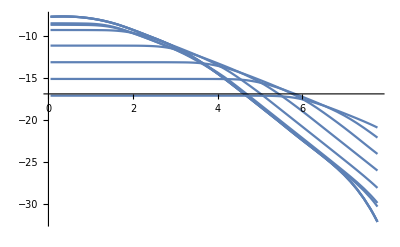

```mathematica
Show[Table[Plot[("σf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{vχ,0.0492,7.78},PlotLegends->("mχ"/.NuclearσDicst10MeVto1PeV[[i,1]]),PlotRange->All],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}]]
```

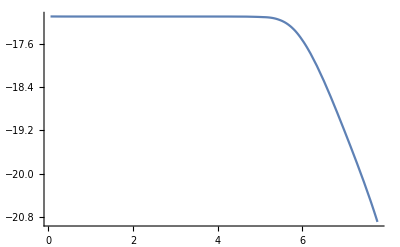

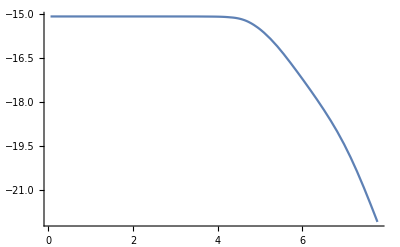

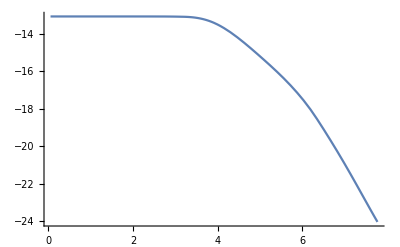

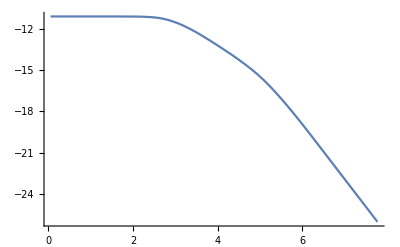

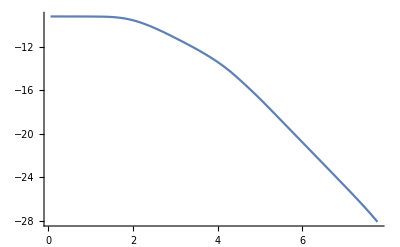

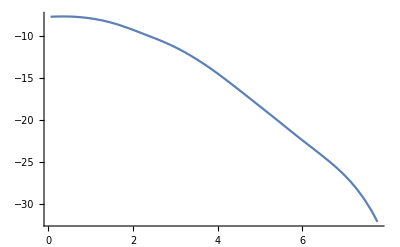

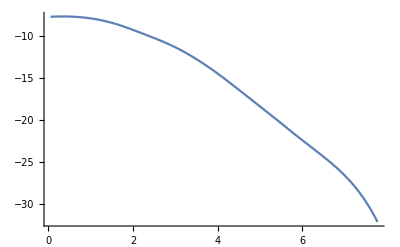

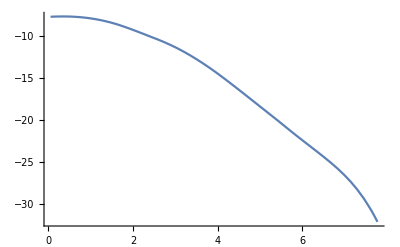

```mathematica
Do[Print@Plot[("σf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{vχ,0.0492,7.78},PlotLegends->("mχ"/.NuclearσDicst10MeVto1PeV[[i,1]]),PlotRange->All],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}]
```

```mathematica
Plot[Table[("σf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],{vχ,0.0492,7.78},PlotLabels->ToString@Table[("mχ"/.NuclearσDicst10MeVto1PeV[[i,1]]),{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],PlotRange->All]
```

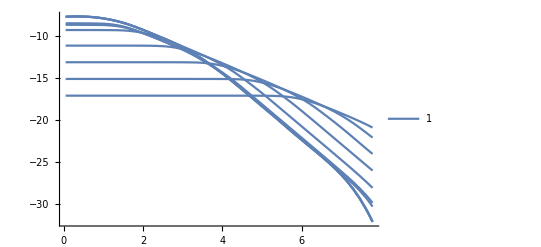

```mathematica
Plot[Table[("σf"/.NuclearσDicst10MeVto1PeV[[i,1]])[vχ],{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],{vχ,0.0492,7.78},PlotLegends->Table[i,{i,Length[NuclearσDicst10MeVto1PeV[[;;,1]]]}],PlotRange->All]
```

### Load Scans

#### From MC

```mathematica
Clear[PDicts1MeVScan]
```

```mathematica
PDicts1MeVScan=ReadIt[NotebookDirectory[]<>"PDicts1MeVScan"];
PDicts10MeVScan=ReadIt[NotebookDirectory[]<>"PDicts10MeVScan"];
PDictsp1GeVScan=ReadIt[NotebookDirectory[]<>"PDictsp1GeVScan"];
PDicts1GeVScan=ReadIt[NotebookDirectory[]<>"PDicts1GeVScan"];
PDicts10GeVScan=ReadIt[NotebookDirectory[]<>"PDicts10GeVScan"];
PDicts100GeVScan=ReadIt[NotebookDirectory[]<>"PDicts100GeVScan"];
PDicts1TeVScan=ReadIt[NotebookDirectory[]<>"PDicts1TeVScan"];
PDicts10TeVScan=ReadIt[NotebookDirectory[]<>"PDicts10TeVScan"];
PDicts100TeVScan=ReadIt[NotebookDirectory[]<>"PDicts100TeVScan"];
PDicts1PeVScan=ReadIt[NotebookDirectory[]<>"PDicts1PeVScan"];
```

#### Get KE Changes

```mathematica
PDicts1MeVKE=IterateKEchange[Flatten@PDicts1MeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10MeVKE=IterateKEchange[Flatten@PDicts10MeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDictsp1GeVKE=IterateKEchange[Flatten@PDictsp1GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1GeVKE=IterateKEchange[Flatten@PDicts1GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10GeVKE=IterateKEchange[Flatten@PDicts10GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts100GeVKE=IterateKEchange[Flatten@PDicts100GeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1TeVKE=IterateKEchange[Flatten@PDicts1TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts10TeVKE=IterateKEchange[Flatten@PDicts10TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts100TeVKE=IterateKEchange[Flatten@PDicts100TeVScan,{0.05},"α"/.Constants`SIConstRepl];
PDicts1PeVKE=IterateKEchange[Flatten@PDicts1PeVScan,{0.05},"α"/.Constants`SIConstRepl];
```

## Definitions

### Utilities

#### Convert from v0 to βD

```mathematica
Clear[v0toβD]
v0toβD[v0_,meD_,mpD_]:=Module[{βD,vpDmean,veDmean},
(*
v0 is the velocity corresponding to the temperature of the aDM particles. By equipartition: 3 Subscript[T, D] = 1/2(Subscript[m, Subscript[e, D]] Subscript[v^2, Subscript[e, D]]+Subscript[m, Subscript[p, D]] Subscript[v^2, Subscript[p, D]]) so we define 3 Subscript[T, D] = m̄ Subscript[v^2, 0] 
*)
βD = 6/((meD + mpD)v0^2);
vpDmean = √(3/(mpD βD));
veDmean = √(3/(meD βD)); 
<|"βD"->βD,"v0"->v0,"vpDmean"->vpDmean,"veDmean"->veDmean|>
]
```

#### Region handling

```mathematica
CrustOrCore[r_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{2,r<("rcore"/.Constants`EarthRepl)}},3](*1 => in the crust, 2 => in the core, 3 => not in the Earth*)
```

```mathematica
SortProcessesByRegion[associationlist_,key_]:=Module[{sortedlist},
sortedlist={{},{},{}}; (*1 corresponds to crust, 2 to core, 3 to outside earth (empty)*)
Do[AppendTo[sortedlist[[("region"/.associationlist[[i]])]],key/.associationlist[[i]]],{i,Length[associationlist]}];
sortedlist
]
```

```mathematica
Clear[RegionΘ]
RegionΘ[r_,regionindex_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{1,r<("rcore"/.Constants`EarthRepl)},{1,r>("rE"/.Constants`EarthRepl)}}[[regionindex;;regionindex]],0]
```

```mathematica
ltor[l_,bE_]:=√(bE^2+l^2)
```

#### Plot P_cap

```mathematica
Clear[PlotPDist]
PlotPDist[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]
```

```mathematica
Clear[PlotPDistEvsNuc]
PlotPDistEvsNuc[PDict_]:=Module[{Pfunc,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
(*Print[mpD];
Print[v0];
PfEs=InterpolatePc[PDict];*)
Do[
Pfunc="PfE"/.PDict[[p]];
κ="κ"/.PDict[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ","Log_10b_E"},PlotLabel->"P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[PDict]}];

Do[
Pfunc="PfNuc"/.PDict[[p]];
κ="κ"/.PDict[[p]];
Print[Show[{DensityPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ","Log_10b_E"},PlotLabel->"P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Pfunc[vχ,bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,Pfunc["Domain"][[2,1]],Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[PDict]}]

]
```

#### Plot KE change

```mathematica
Clear[PlotKEchange]
PlotKEchange[KEchangeMassDicts_]:=Module[{AllbutMassFixed,κ,v0,fD,meDovermpD,plotname},
Do[
AllbutMassFixed=Table[KEchangeMassDicts[[i,j]],{i,Length[KEchangeMassDicts]}];
κ=Union["κ"/.AllbutMassFixed][[1]];

If[κ<10^-7,
v0=Union["v0"/.AllbutMassFixed][[1]];
fD=Union["fD"/.AllbutMassFixed][[1]];
meDovermpD=Union["meD"/.AllbutMassFixed][[1]]/Union["mpD"/.AllbutMassFixed][[1]];

(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);*)
plotname=("Δv_e/((v̄)_e)√((α 0.05)/α_D) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>", Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[ListLinePlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"ΔeKE/vpbar"}/.AllbutMassFixed,AxesLabel->{"Log_10mpD [eV]"},PlotLabel->plotname]];
];
,{j,Dimensions[KEchangeMassDicts][[2]]}];
]
```

```mathematica
Clear[PlotKEchangeκContour]
PlotKEchangeκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];
(*Print[meDovermpD];
Print[v0];*)
(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10FractionBox[SubscriptBox[m,SubscriptBox[e,D]],m_p_D\]="<>ToString[Log10@meDovermpD]);*)
plotname=("Log_10Δv_e/((v̄)_e)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,FrameLabel->{Style["Log_10mpD [eV]",Black,14],Style["κ [ ]",Black,14]},PlotLabel->Style[plotname,Black,12],FrameStyle->Directive[Black,Thickness[0.003]]]];

Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False]}]];

plotname=("Log_10Δv_p/((v̄)_p)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);
Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False]}]]
,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot other parameters

```mathematica
Clear[PlotNcκContour]
PlotNcκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];
(*Print[meDovermpD];
Print[v0];*)
(*plotname=("Δv_e/((v̄)_e)√(α_D/αSuperscriptBox[10, -2]) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>"\n v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1], f_D = "<>ToString[Log10@fD]<>", Log_10FractionBox[SubscriptBox[m,SubscriptBox[e,D]],m_p_D\]="<>ToString[Log10@meDovermpD]);*)
plotname=("Log_10N_c0.05/f_D [ ]- "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Nc"->(AllbutMassandκFixed[[l,k]]["Nc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

```mathematica
Clear[PlotCaptureRateκContour]
PlotCaptureRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,list},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10Γ_capn_aDM0.05/f_D [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;
(*Print[VEarth];*)

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"dNcMaxdt"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"dNcMaxdt"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]}]];

(*Print[ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];*)

(*list ={Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]];
Print[Show[{ListDensityPlot[list,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[list,ContourLabels->All,ContourShading->None,Contours->5,ContourStyle->Black]}]];*)

(*Print[ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["dNcMaxdt"/VEarth]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]];*)

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

```mathematica
Clear[PlotEvaporationRateκContour]
PlotEvaporationRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Γ_evap [s^-1]- "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

(*Print[ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];*)
Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Γtotal"->(AllbutMassandκFixed[[l,k]]["Γtotal"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

```mathematica
(*Clear[PlotNcκContour]
PlotNcκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[
(*AllbutMassFixed=[[i]];*)

(*κ=Union["κ"/.AllbutMassFixed][[1]];*)

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];
(*fD=Union["fD"/.AllbutMassFixed][[1]];*)
meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];

plotname=("N_c0.05/f_D []- "<>" v_0"<>ToString[StringForm["= ``",N@v0/1000]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=(4π)/3("rE")^3/.Constants`EarthRepl;
Print[VEarth];
Print[ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Nc"]}/.AllbutMassandκFixed[[j]]/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]*)
```

#### Plot Energy Fraction of Energy Lost

```mathematica
Clear[PlotELfrac]
PlotELfrac[PDict_]:=Module[{Pfunc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*Electronic*)
Pfunc=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, e))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

(*Nuclear*)
Pfunc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[-Log10@Pfunc[10^vχ,bE],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]
```

```mathematica
Clear[PlotELNucoverE]
PlotELNucoverE[PDict_]:=Module[{PfuncE,PfuncNuc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

PfuncE=ELAveragede[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
PfuncNuc=ELAveragedNuc0[mpD(("c")^2/("JpereV"))^-1/.Constants`SIConstRepl,#1,κ,#2]&;
Print[Show[{DensityPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[10^vχ,bE]/PfuncE[10^vχ,bE]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

,{p,1}](*all κ give the same plot*)
]
```

### MC Processes

#### Gravitational Potential

```mathematica
Vgrav[r_]:=Piecewise[{{-(("G" "ME")/r),r>"rE"/. Constants`EarthRepl},{-(("ME" "G")/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("G" "ME")/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl
```

#### Select Interaction Process

```mathematica
(*σselector[σs_]:=Module[{ξ2,Ps,Psums,Nσ,n},

ξ2 = Random[];

Nσ=Length[σs];
Ps=σs/Total[σs];
Psums=Table[Sum[Ps[[i]],{i,j}],{j,Length[Ps]}];

n=0;
Do[If[ ξ2<=Psums[[i]],n=i;Break[]],{i,1,Nσ}];
(*{n,ξ2,N[Psums]}*)
n
]*)
```

#### Δr total

```mathematica
Clear[ELEarthTot]

fTot0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiO2eELDict[["f"]][mχ,vχ]+10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgOeELDict[["f"]] [mχ,vχ]+10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl
feELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(("ρM")/("ρSiO2")/.MassDensities)(10^SiO2eELDict[["f"]][mχ,vχ])+"MgOFrac"(("ρM")/("ρMgO")/.MassDensities)(10^MgOeELDict[["f"]] [mχ,vχ])]/.EarthRepl 

fNuc0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl (*ignores slight change in densities from surface to mantle in densities (we showed it's irrelevant for iron in the core, so it will be even less significant here)*)

fTot0ELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] + 10^FeNuc0ELDict[["f"]][mχ,vχ]]
feELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] ]
fNuc0ELCore[mχ_,vχ_]:=Log10[10^FeNuc0ELDict[["f"]][mχ,vχ]]

ELEarthTot[r_,mχ_,vχ_]:=Piecewise[{{10^fTot0ELMantle[Log10[mχ], Log10[vχ]],("rE"/.Constants`EarthRepl)> r >=  ("rcore"/.Constants`EarthRepl)},{10^fTot0ELCore[Log10[mχ], Log10[vχ]], ("rcore"/.Constants`EarthRepl)>r}},0]
```

```mathematica
dc[bE_] := 2 √(("rcore")^2-bE^2)/.Constants`EarthRepl (*path length in the core for given impact parameter*)
dE[bE_] := 2 √(("rE")^2-bE^2)/.Constants`EarthRepl (*path length through the earth*)
dM[bE_]:= If[(("rcore")^2/.Constants`EarthRepl)>bE^2,dE[bE] - dc[bE],Re[dE[bE]]](*path length through the Mantle, iff condition is satisfied does it go through the core*)
```

```mathematica
Clear[ΔrAveragedTot0,ΔETot0]

ΔETot0[mχ_,vχ_,κ_,bE_,consts_] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fTot0ELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]])) /.consts ]](*assumes 0 temp nuclear*)

ΔEe[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]])) /.consts ]]

ΔENuc0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl] :=Re[If[(("rcore")^2/.Constants`EarthRepl)>bE^2,(κ^2 "JpereV"(dM[bE] 10^fNuc0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fNuc0ELCore[Log10[mχ], Log10[vχ]])) /.consts,(κ^2 "JpereV"(dM[bE] 10^fNuc0ELMantle[Log10[mχ], Log10[vχ]])) /.consts ]](*assumes 0 temp nuclear*)
EK[mχ_,vχ_] :=1/2 mχ vχ^2
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl,y_:10^-2]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]

ELAveragede[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl]:=  EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]

ELAveragedNuc0[mχ_,vχ_,κ_,bE_,consts_:Constants`SIConstRepl]:=EK[mχ,vχ]/ΔENuc0[mχ,vχ,κ,bE,consts]

fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

**** should put this into a single module for Δr

#### Weak Capture Regime Trajectory

```mathematica
Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_]:=Module[{RE,lsol,ldom,voft},
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχ ELEarthTot[√(bE^2+l[t]^2),mχ,l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

InterpolatingFunction::dmval: Input value {-29.7489,3.77844} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

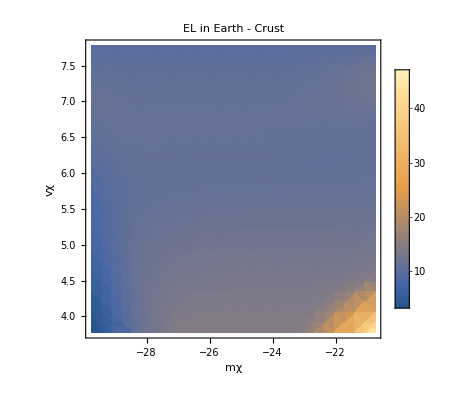

InterpolatingFunction::dmval: Input value {-29.7489,3.77844} lies outside the range of data in the interpolating function. Extrapolation will be used.

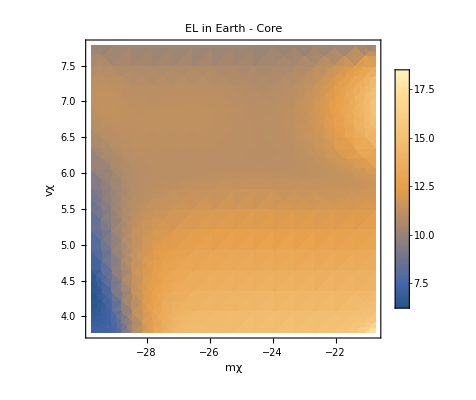

```mathematica
DensityPlot[Log10@ELEarthTot[(5"rE")/6/.Constants`EarthRepl,10^mχ,10^vχ],{mχ,Log10[("JpereV")/("c")^2 10^6/.Constants`SIConstRepl],Log10[("JpereV")/("c")^2 10^15/.Constants`SIConstRepl]},{vχ,Log10[2 10^-5"c"/.Constants`SIConstRepl],Log10[2 10^-1"c"/.Constants`SIConstRepl]},PlotLegends->Automatic,FrameLabel->Automatic,PlotLabel->"EL in Earth - Crust",PlotRange->All]
DensityPlot[Log10@ELEarthTot[("rE")/4/.Constants`EarthRepl,10^mχ,10^vχ],{mχ,Log10[("JpereV")/("c")^2 10^6/.Constants`SIConstRepl],Log10[("JpereV")/("c")^2 10^15/.Constants`SIConstRepl]},{vχ,Log10[2 10^-5"c"/.Constants`SIConstRepl],Log10[2 10^-1"c"/.Constants`SIConstRepl]},PlotLegends->Automatic,FrameLabel->Automatic,PlotLabel->"EL in Earth - Core",PlotRange->All]
```

Current interpolations are going out of range

#### Weak Capture Regime Capture Probability

```mathematica
Clear[GetWeakCaptureProbability]
GetWeakCaptureProbability[lDict_,σDict_]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,tdom,κ,regionindex,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr,SurvivalProb,CaptureProb},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.lDict);
tdom = "domain"/.lDict;
κ=("κ"/.lDict);
regionindex = "regionindex"/.σDict;

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(t)"/.lDict);
vχ=If[vχraw[#]>vχmin,("v(t)"/.lDict)[#],0]&;
χtraj=("l(t)"/.lDict);
bE=("bE"/.lDict);(*impact parameter*)

ξofωandt=Abs[EnergyLoss`ξofωandvχ[#1,ωmin,("v(t)"/.lDict)[#2],mχ,params]-δξ]&;
ωmaxoft=EnergyLoss`ωmaxofvχ[("v(t)"/.lDict)[#1],mχ,params]&;

dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&;

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]])&;

(*Print[("σofξf"/.σDict)[4,Log10[0.1]]];*)

(*
(*Pre ωcapture*)
σoft=If[vχraw[#]>vχmin,("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωmin,ωmaxoft[#]}],0]&;(* ℏ from the jacobians Subscript[E, R]->ω *)
*)

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl))&;

(*Print[ωcapture[50]];*)
(*ω needed to have v < vesc*)
(*σoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωcapture[#],ωmaxoft[#]}],0]&;*)(* ℏ from the jacobians Subscript[E, R]->ω *)

λinvoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],κ^2("ne"/.params)σoftandωmin[#,ωcapture[#]],0]&;

(*Print[("κ"/.lDict)];
Print[("ne"/.params)];*)

(*Print[Log10@vχ[50]];
Print[Log10@ξofωandt[#2,#1]]&[50,ωcapture[50]];
Print[("σofξf"/.σDict)[Log10@vχ[50],Log10@ξofωandt[#2,#1]&[50,ωcapture[50]]]];
Print[("σofξf"/.σDict)[4,Log10[0.1]]];
Print[("σofξf"/.σDict)[4.298535219512971,-0.00005598166375369483]]*)
(*Print[("σofξf"/.σDict)];
Print[("σofξf"/.σDict)[4.298535219512971,-0.00005598166375369483]];*)
(*Print[λinvoft];
Print[σoftandωmin[#,ωcapture[#]]&[50]];
Print[(("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]])&[50,ωcapture[50]]];
Print[("σofξf"/.σDict)];*)
(*Print[Plot[λinvoft[t]/(("κ"/.lDict)^2("ne"/.params)),{t,tdom[[1]],tdom[[2]]}]];
Print[Plot[λinvoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}]];*)

(*Print["tdom is ",Round[tdom[[2]]]];
Print[λinvoft[50]vχ[50]];*)

(*integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];*)
integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t]RegionΘ[ltor[χtraj[t],bE],regionindex],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];

(*integralofλinvwrtr=NIntegrate[λinvoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)
(* vχ from the jacobians l -> t - do simple numerical integral here, Nintegrate was giving some weird divergin issues*)
(*SurvivalProb =E^-integralofλinvwrtr;
CaptureProb=1-SurvivalProb;*)

(*Print[integralofλinvwrtr];*)
(*Print["Starting Nintegrate"];
Print@NIntegrate[σoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)

(*<|"SurvivalProb"->SurvivalProb,"CaptureProb"->CaptureProb|>*)
integralofλinvwrtr
]
```

-Graphics-

We run into this issue when we try to use NIntegrate for the survival probability integral

```mathematica
Clear[GetWeakCaptureProbabilityNuc]
GetWeakCaptureProbabilityNuc[lDict_,σDict_]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,tdom,κ,regionindex,mN,ωcapture,δξ,ξofωandt,ωmaxoft,dσdERoftandω,σoftandωmin,λinvoft,integralofλinvwrtr},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.lDict);
tdom = "domain"/.lDict;
κ=("κ"/.lDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;

(*Print[mN];*)

vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχraw=("v(t)"/.lDict);
vχ=If[vχraw[#]>vχmin,("v(t)"/.lDict)[#],0]&;

χtraj=("l(t)"/.lDict);
bE=("bE"/.lDict);(*impact parameter*)

ξofωandt=Abs[EnergyLoss`ξofωNuc[#1,ωmin,("v(t)"/.lDict)[#2],mχ,mN,params]-δξ]&;
ωmaxoft=EnergyLoss`ωmaxNuc[("v(t)"/.lDict)[#1],mχ,mN,params]&;

dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&;

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]])&;

(*Print[("σofξf"/.σDict)[4,Log10[0.1]]];*)

(*
(*Pre ωcapture*)
σoft=If[vχraw[#]>vχmin,("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωmin,ωmaxoft[#]}],0]&;(* ℏ from the jacobians Subscript[E, R]->ω *)
*)

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - ("vesc"/.Constants`EarthRepl))&;

(*Print[ωcapture[50]];*)
(*ω needed to have v < vesc*)
(*σoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],("κ"/.lDict)^2("ne"/.params)NIntegrate[ dσdERoftandω[#,ω]("ℏ"/.params),{ω,ωcapture[#],ωmaxoft[#]}],0]&;*)(* ℏ from the jacobians Subscript[E, R]->ω *)

λinvoft=If[vχraw[#]>vχmin && ωmaxoft[#]>ωcapture[#],κ^2("nI"/.NucleusParams)σoftandωmin[#,ωcapture[#]],0]&;

(*Print[("κ"/.lDict)];
Print[("ne"/.params)];*)

(*Print[Log10@vχ[50]];
Print[Log10@ξofωandt[#2,#1]]&[50,ωcapture[50]];
Print[("σofξf"/.σDict)[Log10@vχ[50],Log10@ξofωandt[#2,#1]&[50,ωcapture[50]]]];
Print[("σofξf"/.σDict)[4,Log10[0.1]]];
Print[("σofξf"/.σDict)[4.298535219512971,-0.00005598166375369483]]*)
(*Print[("σofξf"/.σDict)];
Print[("σofξf"/.σDict)[4.298535219512971,-0.00005598166375369483]];*)
(*Print[λinvoft];
Print[σoftandωmin[#,ωcapture[#]]&[50]];
Print[(("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]])&[50,ωcapture[50]]];
Print[("σofξf"/.σDict)];*)
(*Print[Plot[λinvoft[t]/(("κ"/.lDict)^2("ne"/.params)),{t,tdom[[1]],tdom[[2]]}]];
Print[Plot[λinvoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}]];*)

(*Print["tdom is ",Round[tdom[[2]]]];
Print[λinvoft[50]vχ[50]];*)

integralofλinvwrtr=Total@Table[λinvoft[t]vχ[t]RegionΘ[ltor[χtraj[t],bE],regionindex],{t,Round[tdom[[1]]],Round[tdom[[2]]],1}];
(*integralofλinvwrtr=NIntegrate[λinvoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)
(* vχ from the jacobians l -> t - do simple numerical integral here, Nintegrate was giving some weird divergin issues*)
(*
SurvivalProb =E^-integralofλinvwrtr;
CaptureProb=1-SurvivalProb;*)
(*Print[integralofλinvwrtr];*)
(*Print["Starting Nintegrate"];
Print@NIntegrate[σoft[t]vχ[t],{t,tdom[[1]],tdom[[2]]}];*)

(*<|"SurvivalProb"->SurvivalProb,"CaptureProb"->CaptureProb,|>*)
integralofλinvwrtr
]
```

### Initial Conditions

```mathematica
Clear[GetvχMax]
GetvχMax[Pcut_,βD_,mχ_]:=Module[{oneminusCDFvmax,vesc},
vesc=("vesc"/.Constants`EarthRepl);
oneminusCDFvmax = ⅇ^(1/2 mχ vesc^2 βD) (1+2 ⅇ^(-1/2 mχ vmax^2 βD) √((mχ βD)/(2 π))vmax- Erf[√((mχ βD)/(2 π))vmax] );(*Integral of MB dist, from Subscript[v, max] to ∞ - so probability of v >= Subscript[v, max]*)
vmax/.NSolve[{Pcut==oneminusCDFvmax&&0<vmax<10^6},vmax][[1]]
]
```

```mathematica
Integrate[ ⅇ^(-1/2 m (v^2-vesc^2) β) √(2/π) v^2 (m β)^(3/2) ,{v,vmax,∞}]
%//Normal//PowerExpand//Simplify
```

ConditionalExpression[(ⅇ^(1/2 m vesc^2 β) (m β)^(3/2) (2 ⅇ^(-1/2 m vmax^2 β) m vmax β+√(2 π) √(m β)-√m √(2 π) √β Erf[(√m vmax √β)/(√2)]))/(m^2 √(2 π) β^2), Re[m β]>0]

(ⅇ^(1/2 m vesc^2 β) (√(2 π)+2 ⅇ^(-1/2 m vmax^2 β) √m vmax √β-√(2 π) Erf[(√m vmax √β)/(√2)]))/(√(2 π))

```mathematica
Clear[GetvχatEarth]
GetvχatEarth[mχ_,βD_,vχMax_,V_:Vgrav,nbs_:10,nvχs_:30,lowerbrat_:10^-6]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},

    rE = "rE"/.Constants`EarthRepl;
    vmin = "vesc"/.Constants`EarthRepl;
    vχs = 10^Subdivide[Log10@vmin,Log10@vχMax,nvχs];
    (*bs = 10^Subdivide[Log10[lowerbrat rE],Log10@rE,nbs];*)
bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]
```

### Get Capture Probability

New Psuedocode:

pass the initial conditions and κ to get capture rate

```mathematica
Clear[GetCaptureRate]
GetCaptureRate[meDovermpD_,κ_,v0_,σDictsElectronic_,σDictsNuclear_]:= Module[{mpD,meD,βD,v0pD,vχMax,ICdict,Δrbyκsquared,RE,TrajDict,vfinal,captured,integralofλinvwrtrE ,integralofλinvwrtrNuc,SurvivalProb,CaptureProb,PDictList={}},

mpD=Join["mχ"/.σDictsElectronic,"mχ"/.σDictsNuclear];
mpD=If[Length@Union[mpD]==1,mpD[[1]],Print["mχ must be the same in all processes:",mpD];Return[<||>,Module]];
meD = meDovermpD mpD;

(*Print@v0toβD[v0,meD,mpD];*)

βD ="βD"/.v0toβD[ v0,meD,mpD];

vχMax=GetvχMax[10^-4,βD,mpD];
(*Print[vχMax];*)

(*Print[v0];
Print[meDovermpD];*)

ICdict=Flatten@GetvχatEarth[mpD,βD,vχMax];(*dictionary of initial conditions at earth*)

(*Print[ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],1+Log10[ "χspeedEarth"]/.ICdict];*)
(*Print@fTot0ELCore[Log10[mpD],2+Log10[ "χspeedEarth"]/.ICdict];
(*Print@dM["bEarth"/.ICdict];*)
Print@dc["bEarth"/.ICdict];
Print[("rcore"/.Constants`EarthRepl)>("bEarth"/.ICdict)^2];*)
(*"JpereV"ΔETot0[mpD,"χspeedEarth"/.ICdict,κ,"bEarth"/.ICdict,Constants`SIConstRepl]/.Constants`SIConstRepl*)
Monitor[
Do[
Δrbyκsquared=ΔrAveragedTot0[mpD,"χspeedEarth"/.ICdict[[n]],1,"bEarth"/.ICdict[[n]]];
RE=dE["bEarth"/.ICdict[[n]]];

(*Print@Δrbyκsquared;*)
(*Print@(Δrbyκsquared/RE);*)
(*κStrongWeakBoundary=κt/.Solve[Δrbyκsquared/κt^2==RE/100,κt][[2]];*)
(*Print[ELEarthTot[r,mpD,"χspeedEarth"/.ICdict]/.r->1/2"rE"/.Constants`EarthRepl];*)
(*Plot[(ELEarthTot[#,mpD,"χspeedEarth"/.ICdict])&[r],{r,1,"rE"/.Constants`EarthRepl}];*)

If[Δrbyκsquared/κ^2>RE/100,

TrajDict=GetWeakCaptureTrajectory[mpD,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ];
(*Print[Plot["l(t)"[t]/.TrajDict,{t,0,TrajDict["domain"][[2]]}]];
Print[Plot["v(t)"[t]/.TrajDict,{t,0,TrajDict["domain"][[2]]}]];
*)
vfinal= ("v(t)"/.TrajDict)[TrajDict["domain"][[2]]];
captured=vfinal<"vesc"/.Constants`EarthRepl;

(*captured=False;*)
(*If[captured,Print["Captured"]];*)

(*σdict = Fe2eDictUnitTest;*)
If[!captured,
integralofλinvwrtrE = Total@Table[GetWeakCaptureProbability[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];

integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNuc[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];

(*put get NcMax here*)

SurvivalProb =E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc));
CaptureProb=1-SurvivalProb;
AppendTo[PDictList,<|"Psurv"->N@SurvivalProb,"Pcap"->Max[CaptureProb,10^-30],"CSDcap"->captured,"vχE"->"χspeedEarth"/.ICdict[[n]],"bEarth"->("bEarth"/.ICdict[[n]]),"vfinal"->vfinal,"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->Max[1-E^-integralofλinvwrtrE,10^-30],"PcapNuc"->Max[1-E^-integralofλinvwrtrNuc,10^-30],"intλinvE"->integralofλinvwrtrE,"intλinvNuc"->integralofλinvwrtrNuc|>];,
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->vfinal,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->30,"intλinvNuc"->30|>]
];
,
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->0,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->30,"intλinvNuc"->30|>]
];
,{n,Length[ICdict]}
];
,n];
PDictList
]
```

```mathematica
Clear[IterateGetCaptureRate]
IterateGetCaptureRate[meDovermpD_,κs_,v0_,σDictsElectronic_,σDictsNuclear_]:= Module[{PDictList={}},

Monitor[
Do[PDictList=Join[PDictList,GetCaptureRate[meDovermpD,κs[[κ]],v0,σDictsElectronic,σDictsNuclear]],{κ,Length[κs]}];
,κ];

(*NotCSDcaptured = {};
Do[If[!"CSDcap"/.PDictList[[i]],AppendTo[NotCSDcaptured,PDictList[[i]]]],{i,Length[PDictList]}];
*)
(*<|"AllDicts"->PDictList,"NotCSDStopped"->NotCSDcaptured|>*)
(*<|"AllDicts"->PDictList|>*)
PDictList
]
```

```mathematica
Clear[InterpolatePc]
InterpolatePc[PDictList_]:=Module[{Intertable,Interf,κGatheredDicts,mpD,meD,vχMax,βD,v0},

{mpD,meD,vχMax,βD,v0}=Union[{"mpD","meD","vχMax","βD","v0"}/.PDictList][[1]];
κGatheredDicts=Gather[PDictList,(#1["κ"]==#2["κ"])&];
Interf=Table[<|"Pf"->Interpolation[Log10@{{"vχE","bEarth"},"Pcap"}/.κGatheredDicts[[i]],InterpolationOrder->1],"κ"->(Union["κ"/.κGatheredDicts[[i]]][[1]]),"mpD"->mpD,"meD"->meD,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"PfE"->Interpolation[Log10@{{"vχE","bEarth"},"PcapE"}/.κGatheredDicts[[i]],InterpolationOrder->1],"PfNuc"->Interpolation[Log10@{{"vχE","bEarth"},"PcapNuc"}/.κGatheredDicts[[i]],InterpolationOrder->1]|>,{i,Length[κGatheredDicts]}];
Interf
]
```

### Get Total Capture Rate

#### Flux and NcMax defn

```mathematica
nD0ΛCDM[fD_,mDMtot_] := Module[{ΛCDMrepl,h,ρcritbaumanncm,ρcritbaumannm, n0,mSMtot,ρDM0},
ΛCDMrepl= {"Ωk" ->0.00,"Ωr"->9.4 10^-5, "Ωm"->0.32,"ΩΛ"->0.68,"Ωb"->0.05,"Ωc"->0.27}; (*[] ΛCDM density parameters*)
h= 0.67; (*baumann 1.2.64*)

ρcritbaumanncm = 1.1 10^-5 h^2; (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  (10^6); (*[protons m^-3]*)

n0 = "Ωb" ρcritbaumannm /.ΛCDMrepl;  (*[m^-3] proton / electron number density today*)
mSMtot= "m" + 2000 "m"/.Constants`SIConstRepl;

ρDM0= "Ωc"/"Ωb" n0 mSMtot/.ΛCDMrepl;
ρDM0/mDMtot fD
]
```

```mathematica
(*GetFluxAtEarth[mχ_,βD_,nD_]:=Module[{},
(*nD is the local aDM number density*)
(ⅇ^(1/4 mχ ("vesc")^2 βD) √mχ nD ("vesc")^2 √βD BesselK[1,1/4 mχ ("vesc")^2 βD])/(2 √(2 π))/.Constants`EarthRepl
]*)
```

```mathematica
(*Clear[GetNcMax]
GetNcMax[Pcapbar_,mχ_,βD_,nD_]:=Module[{tEarth,AEarth,dNcMaxdt,NcMax},
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π ("rE")^2/.Constants`EarthRepl; (*[m^2] Area of the Earth*)
dNcMaxdt = Pcapbar AEarth GetFluxAtEarth[mχ,βD,nD];(*capture rate of aDM*)
NcMax = tEarth dNcMaxdt;
<|"NcMax"->NcMax,"dNcMaxdt"->dNcMaxdt|>
]*)
```

```mathematica
Clear[GetNcMax]
GetNcMax[IGCRDict_]:=Module[{InterPDicts,Pfs,rE,vesc,tEarth,AEarth,mχ,βD,Pfdom,fintegrand,dNcMaxdt,db=10^-4("rE"/.Constants`EarthRepl)},
(*Get maximum possible accumulation over the lifetime of Earth, with κ=1*)

InterPDicts=InterpolatePc[IGCRDict];
Pfs="Pf"/.InterPDicts;

rE="rE"/.Constants`EarthRepl;
vesc = "vesc"/.Constants`EarthRepl;
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π rE^2; (*[m^2] Area of the Earth*)

Do[
mχ="mpD"/.InterPDicts[[i]];
βD="βD"/.InterPDicts[[i]];
Pfdom=Pfs[[i]]["Domain"];
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[NIntegrate[#^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + #^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@#],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}]&[bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}];*)
(*dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[Total@Table[db bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,Round[10^Pfdom[[2,1]]],Round[10^Pfdom[[2,2]]],Round[db]}],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}];*)
fintegrand[vχ_?NumberQ]:=NIntegrate[bE^2 ⅇ^(-1/2 mχ (vχ^2-vesc^2) βD)  vχ^3/(√(1 + bE^2/rE^2))10^Pfs[[i]][Log10@vχ,Log10@bE],{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]}];
dNcMaxdt=AEarth(3 "nD" √(2/π)  (mχ βD)^(3/2))/rE^3 NIntegrate[fintegrand[vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,2]]}];
AppendTo[InterPDicts[[i]],<|"dNcMaxdt"->dNcMaxdt|>];
AppendTo[InterPDicts[[i]],<|"NcMax"->dNcMaxdt tEarth|>];
,{i,Length[Pfs]}];
InterPDicts
]
```

#### Evaporation Rate

```mathematica
Clear[GetEvaporationRate]
GetEvaporationRate[σDict_]:= Module[{vχmin,vχmax,mχ,ωmin,params,regionindex,NucleusParams,mN,nT,βE,ωcapture,δξ,ξofωandvχ,ωmaxofvχ,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mN = "mN"/.σDict;
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "nI"/.NucleusParams;
 
(*Print[mχ("c")^2/("JpereV")/.SIConstRepl];
Print[√(2/(mχ βE))];
Print[1/βE 1/("JpereV")/.SIConstRepl];*)

ξofωandvχ=Abs[EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]-δξ]&;

(*dσdERofvχandω=10^Re@("dσf"/.σDict)[Log10@#1,Log10@ξofωandvχ[#2,#1]]&;*)

σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@ξofωandvχ[#2,#1]]])&;

(*vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; (*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
vχmaxofvχ =(2 ("ℏ"/.params))/mχ ωmaxofvχ[#]&;*)
vχmin = 10^(("σofξf"/.σDict)["Domain"][[1,1]]);
(*vχmax=  10^(("σofξf"/.σDict)["Domain"][[1,2]]);*)

(*Post ωcapture*)
ωmaxofvχ=EnergyLoss`ωmaxNuc[#1,mχ,mN,params]&;
(*ωcapture = Max[1/(2 ("ℏ"/.params))mχ (("vesc"/.Constants`EarthRepl)^2-#^2 ),1/(2 ("ℏ"/.params))mχ vχmin^2]&;*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (("vesc"/.Constants`EarthRepl)^2-#^2 )&;(*We are going outside the range of the interpolating function at times. *)

(*Print[Solve[ω==ωmaxofvχ[vχ]]];*)


vχstωcapisωmax=vχ/.NSolve[ωmaxofvχ[vχ]==ωcapture[vχ],vχ][[2]];


ΩevapperparticlewvT=nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π NIntegrate[vT^2 E^(-βE 1/2 mN vT^2)Total@Table[((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2)HeavisideTheta[ωmaxofvχ[vχ]-ωcapture[vχ]]σofvχandωmin[vχ,ωcapture[vχ]],{vχ,Round[vχstωcapisωmax],Round["vesc"/.Constants`EarthRepl]}],{vT,0,∞}];(*first factor in table comes from integral of |vT - vχ| over cosθ *)


RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}];
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3;
(*Print[RegionVolume];*)
Γevappercapturedparticle=ΩevapperparticlewvT RegionVolume/EarthVolume; (*Γκ^2 corresponds to Revp in appendix*)(*Assumes homogeneously distributed aDM in the Earth*)

Γevappercapturedparticle
]
```

```mathematica
Clear[IterateGetEvaporationRate]
IterateGetEvaporationRate[NuclearσDicts_]:=Module[{Γlist={},ΓTotal},
Monitor[
Do[
AppendTo[Γlist,GetEvaporationRate[NuclearσDicts[[n]]]],
{n,Length[NuclearσDicts]}
];
,n];
ΓTotal=Total[Γlist];
<|"ΓTotal"->ΓTotal,"Γs"->Γlist|>
]
```

#### Get N_c in the presence of evaporation

```mathematica
Clear[GetNc]
GetNc[NcMaxDictList_,NucσDict_]:=Module[{indexforcapturethreshold,κ,NcMax,dNcMaxdt,Γtotal,tE,timeenoughforequil,Nc,tempNcDict={},NcDicts={}},
Γtotal="ΓTotal"/.IterateGetEvaporationRate[NucσDict];(*evaporation rate per captured particle assuming homogeneous distribution in the Earth - Conservative: it is dominated by the core, the lower g there will reduce the number density*)
(*Print[Γtotal];*)
Do[
(*Print[NcMaxDictList[[i]]];*)
NcMax="NcMax"/.NcMaxDictList[[i]];
dNcMaxdt="dNcMaxdt"/.NcMaxDictList[[i]];
tE=NcMax/dNcMaxdt;(*[s] age of the Earth*)

κ="κ"/.NcMaxDictList[[i]];
(*Print[Γtotal];
Print[κcaptures^2 Γtotal ];
Print[(κcaptures^2 Γtotal )[[1]]];
Print[Table[(κcaptures^2 Γtotal )[[i]],{i,Length[κcaptures]}]];*)
timeenoughforequil=1/tE<(κ^2 Γtotal);(*has had time to equilibrate if age of Earth is greater than evaporation time scale*)
(*Print[timeenoughforequil];*)
(*tempNcDict = Append[NcMaxDictList[[i]],<||>];*)
(*Print[NcMaxDictList[[i]]];*)
(*Nc=If[timeenoughforequil,dNcMaxdt/Γtotal,κ^2 NcMax ];*)(*both per particle evaporation and capture rates scale as κ^2, so in equilibirium, the captured number is independent of it ---- WRONG!!!*)
Nc=If[timeenoughforequil,dNcMaxdt/(κ^2 Γtotal),NcMax ];(*both per particle evaporation and capture rates scale as κ^2, so in equilibirium, the captured number is independent of it ---- WRONG!!!*)
(*Print[Nc];*)

tempNcDict = Append[NcMaxDictList[[i]] ,{"timeenoughforequil"->timeenoughforequil,"Nc"->Nc,"Γtotal"->Γtotal}];
AppendTo[NcDicts,tempNcDict];
,{i,Length[NcMaxDictList]}];
NcDicts
]
```

#### Scan parameter space

```mathematica
Clear[ScanGetCaptureRateandGetNc]
ScanGetCaptureRateandGetNc[meDratios_,κs_,v0s_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{PDictList,PDictLists={},ScanDictList={},meDratio,v0,mpD,βD,NcMaxDict,NcDict},
mpD= "mχ"/.ElectronicσDicsts[[1]];
Print["mpD: ",mpD( ("JpereV")/("c")^2)^-1/.Constants`SIConstRepl];
Do[
meDratio=("meD/mpD"/.meDratios[[m]]);
v0 = v0s[[n]];
βD ="βD"/.v0toβD[v0,meDratio mpD,mpD];
Print["meD/mpD: ",meDratio];
Print["v0: ",v0];
Print["βD: ",βD];

PDictList=IterateGetCaptureRate[meDratio,κs,v0,ElectronicσDicsts,NuclearσDicts];
(*AppendTo[PDictLists,PDictList];*)
PlotPDist[PDictList];

NcMaxDict=GetNcMax[PDictList];
NcDict=GetNc[NcMaxDict,NuclearσDicts];

AppendTo[ScanDictList, NcDict];
(*AppendTo[ScanDictList,{v0,meDratio}];*)

(*AppendTo[ScanPointInfoList,<|"Pcaps"->κPtable[[;;,2]],"κs"->κPtable[[;;,1]],"NcMaxes"->("NcMax"/.NcMaxes),"dNcMaxdt"->("dNcMaxdt"/.NcMaxes),"βD"->βD,"v0"->v0,"meD/mpD"->meDratio,"mpD"->mpD|>];*)
,{m,Length[meDratios]},{n,Length[v0s]}];

(*<|"PDictLists"->PDictLists,"ScanDictList"->ScanDictList|>*)
ScanDictList
]
```

### Get Significant Capture Regimes

#### KE Change

```mathematica
VCoulombE[N_,αD_]:=αD/("α")("e")^2/(4 π "ϵ0")N/("rE")/.Constants`EarthRepl/.Constants`SIConstRepl
```

```mathematica
(*Clear[KEchange]
KEchange[NmaxnD0is1_,fD_,αD_,mpD_,meDratio_]:=Module[{Ntot,pDvescchange,eDvescchange},

Ntot = nD0ΛCDM[fD,mpD(1+meDratio)]NmaxnD0is1;
pDvescchange=√((2 VCoulombE[Ntot,αD])/mpD); 
eDvescchange=√((2 VCoulombE[Ntot,αD])/(meDratio mpD));
<|"pDvescchange"->pDvescchange,"eDvescchange"->eDvescchange,"Ntot"->Ntot|>
]*)
```

```mathematica
Clear[KEchange]
KEchange[ScanDict_,fD_,αD_]:=Module[{mpD,meD,nD0,Nc,Ntot,pDvescchange,eDvescchange,pDKEfracchange,eDKEfracchange},
{mpD,meD}={"mpD","meD"}/.ScanDict;
(*Print[mpD," ",meD];*)
nD0=nD0ΛCDM[fD,mpD +meD];

Nc="Nc"/.ScanDict;
Ntot = Nc/."nD"->nD0;

pDvescchange=√((2 VCoulombE[Ntot,αD])/mpD); 
eDvescchange=√((2 VCoulombE[Ntot,αD])/meD);
pDKEfracchange=pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict;
eDKEfracchange=eDvescchange/(√(("vesc")^2+3/("βD" meD)))/.Constants`EarthRepl/.ScanDict;
(*Print[pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict];*)
Append[ScanDict,{"pDvescchange"->pDvescchange,"eDvescchange"->eDvescchange,"ΔpKE/vpbar"->pDKEfracchange,"ΔeKE/vpbar"->eDKEfracchange,"Ntot"->Ntot,"nD"->nD0,"fD"->fD,"αD"->αD}]
]
```

```mathematica
Clear[IterateKEchange]
IterateKEchange[ScanDicts_,fDs_,αD_]:=Module[{KEchangeDicts={}},
Do[
AppendTo[KEchangeDicts,KEchange[ScanDicts[[i]],fDs[[j]],αD]];
,{i,Length[ScanDicts]},{j,Length[fDs]}];
KEchangeDicts
]
```

## Run

#### Scan over the masses 0.1 GeV to 10 GeV - Post κ Bug Fix

switch to linear subdividing for impact parameter

mpD: 1.×10^8

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^19

InterpolatingFunction::dmval: Input value {-27.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 573.809, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 614.262, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 658.83, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^8

20000

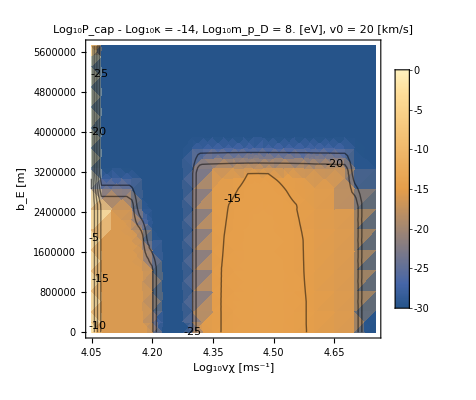

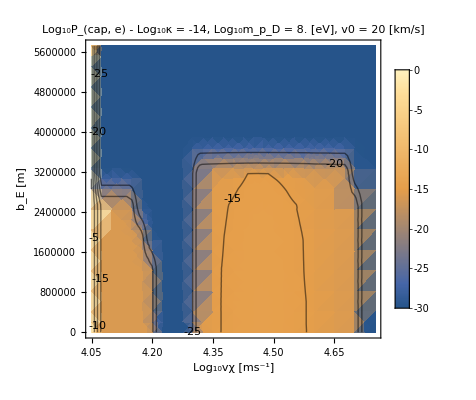

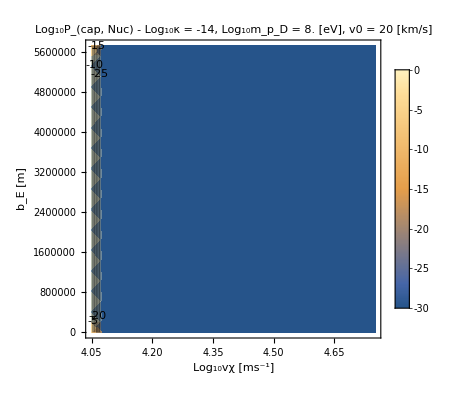

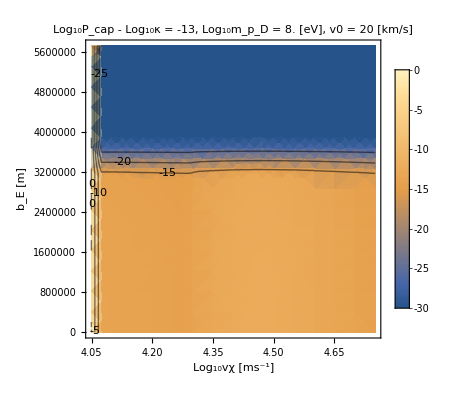

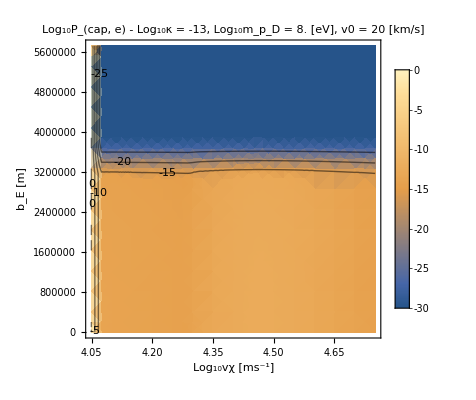

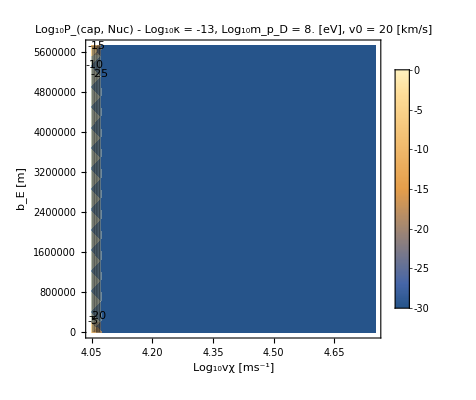

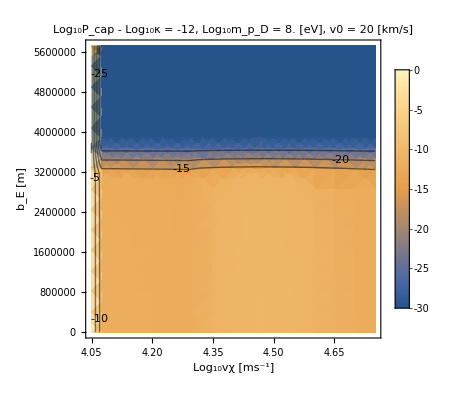

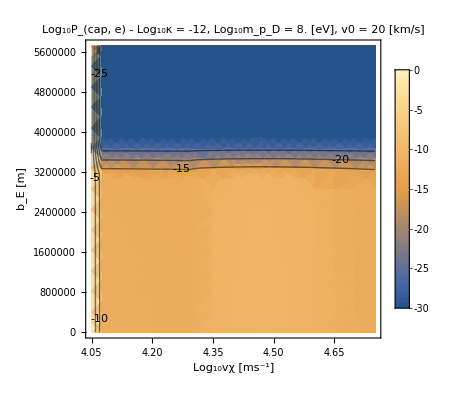

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19568.2}. NIntegrate obtained 7.58756×10^35 and 1.50255×10^31 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^17

1.×10^8

220000

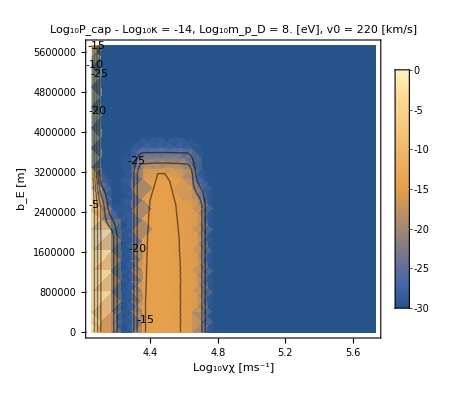

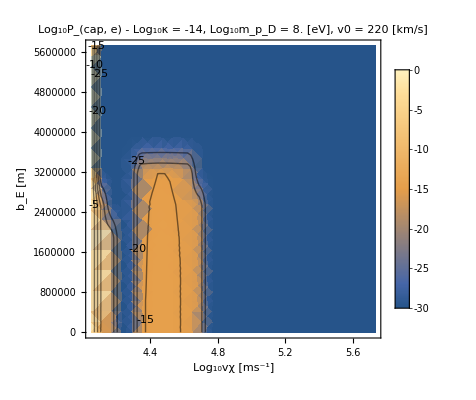

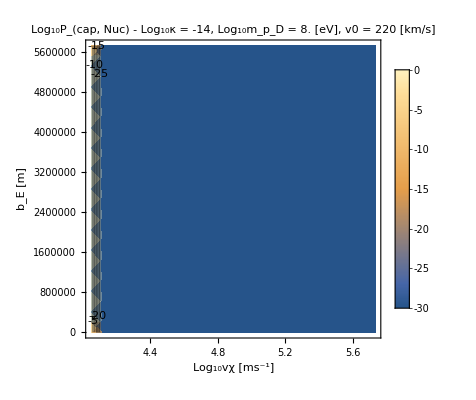

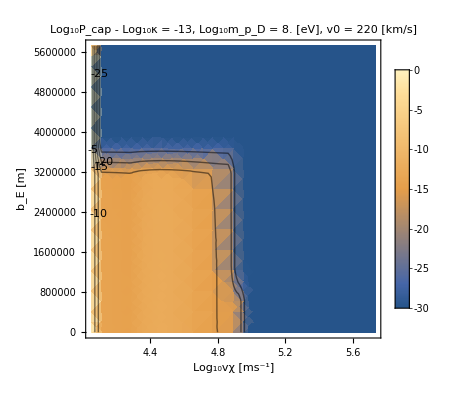

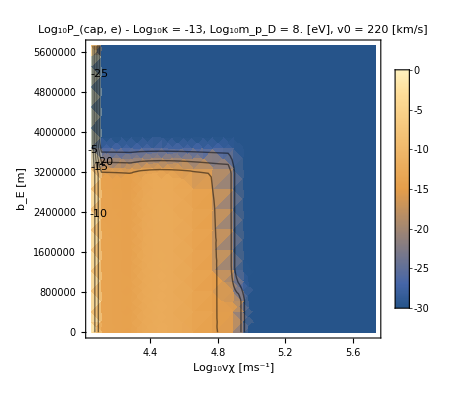

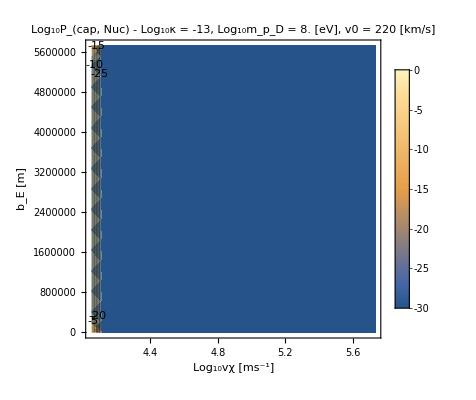

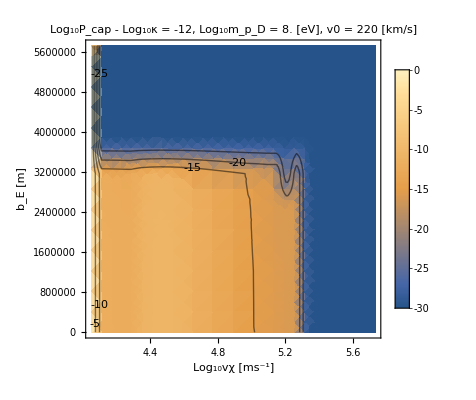

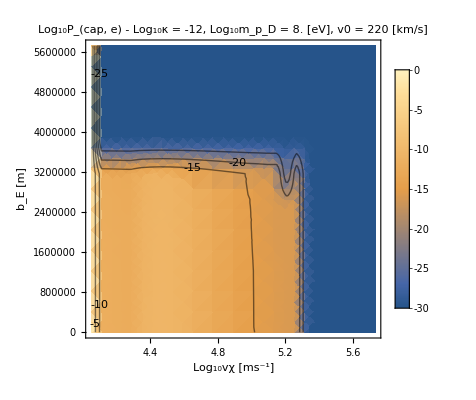

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21876.735141836}. NIntegrate obtained 3.04267×10^36 and 2.85934×10^33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {83774.4}. NIntegrate obtained 8.7922×10^38 and 1.4873×10^35 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^19

1.×10^8

20000

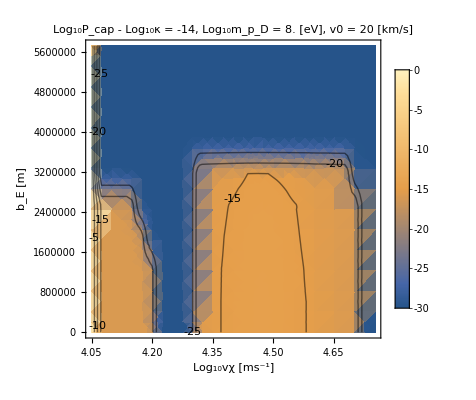

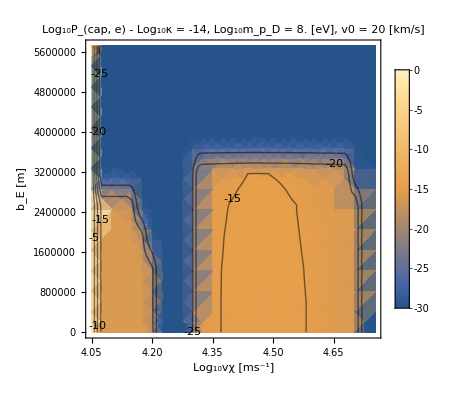

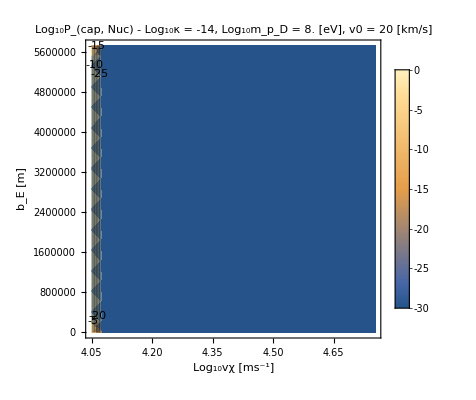

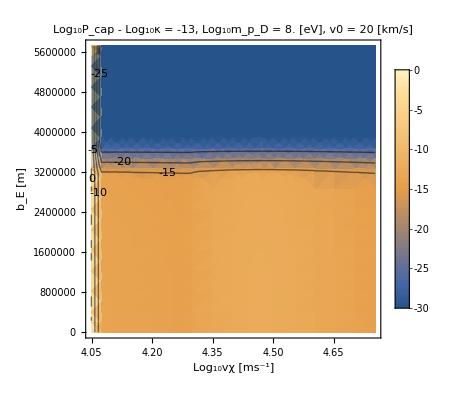

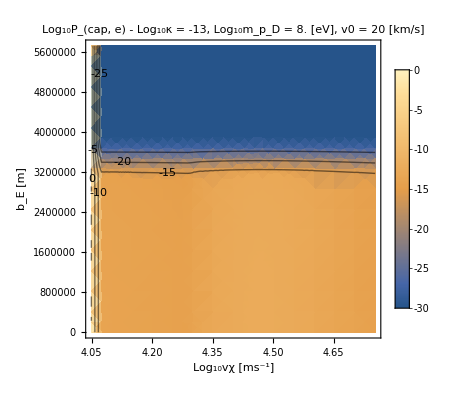

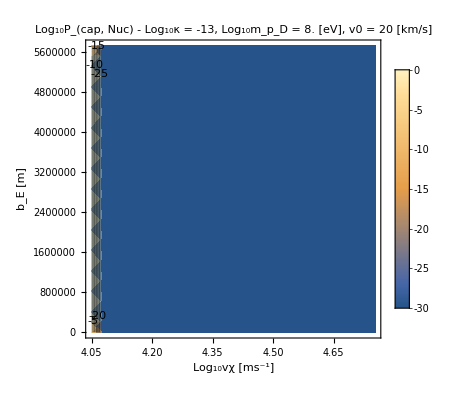

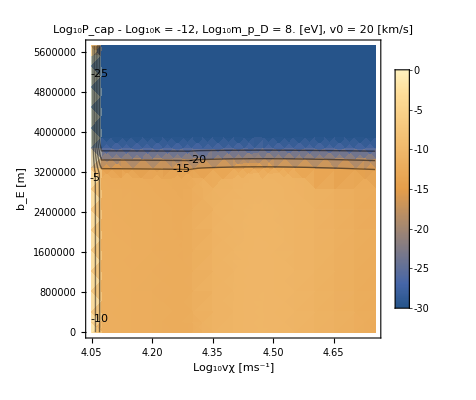

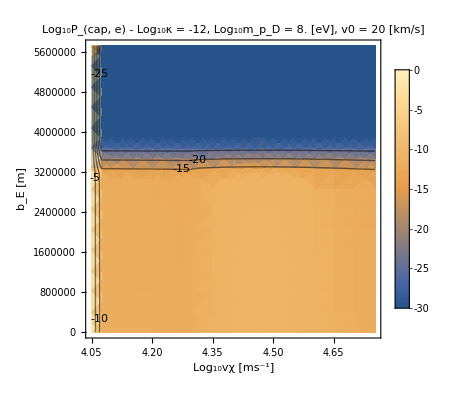

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^17

1.×10^8

220000

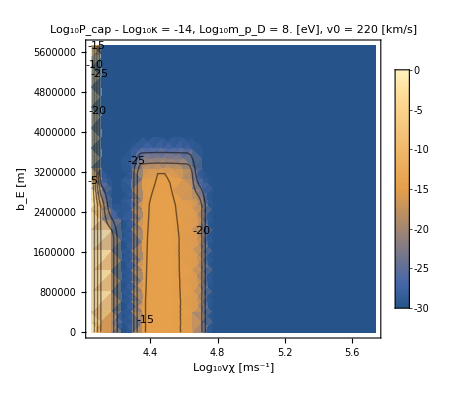

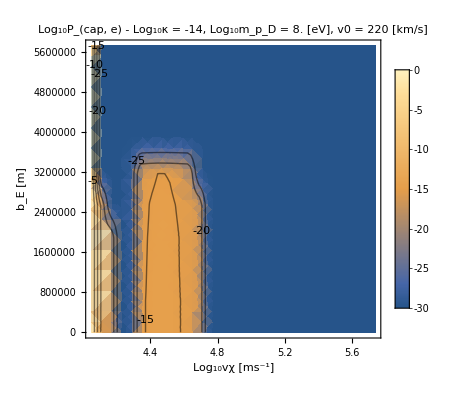

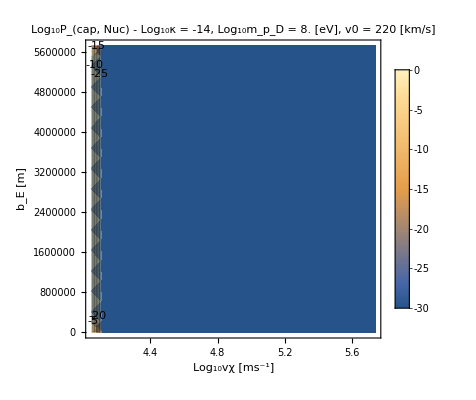

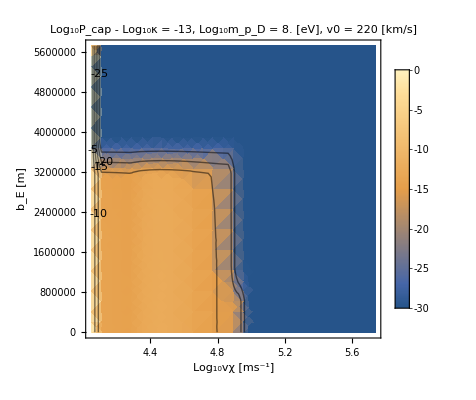

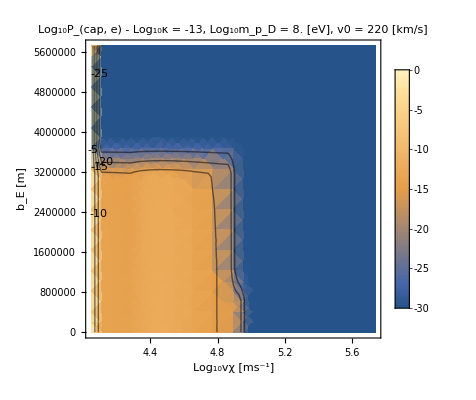

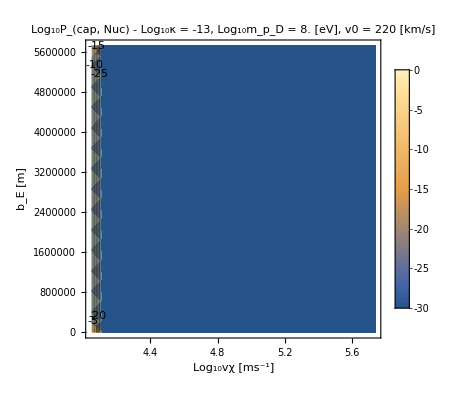

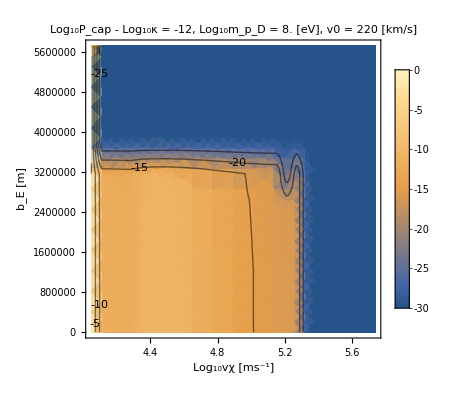

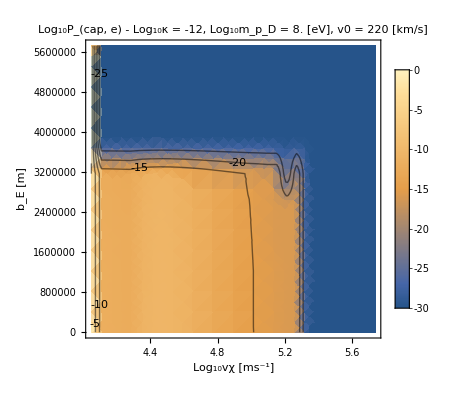

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.40135×10^15 nD,NcMax→8.94496×10^32 nD,timeenoughforequil→True,Nc→1.88789×10^27 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.25533×10^15 nD,NcMax→1.01383×10^33 nD,timeenoughforequil→True,Nc→2.13975×10^25 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.70843×10^15 nD,NcMax→1.07714×10^33 nD,timeenoughforequil→True,Nc→2.27338×10^23 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.332×10^15 nD,NcMax→1.16428×10^33 nD,timeenoughforequil→True,Nc→2.45728×10^21 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.58018×10^18 nD,NcMax→9.19484×10^35 nD,timeenoughforequil→True,Nc→1.94063×10^22 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→2.29356×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→2.29356×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→59528.1,βD→8.42612×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→2.29356×10^16 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16375×10^13 nD,NcMax→1.62617×10^30 nD,timeenoughforequil→True,Nc→3.43215×10^24 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.31926×10^13 nD,NcMax→1.84347×10^30 nD,timeenoughforequil→True,Nc→3.89077×10^22 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.40276×10^13 nD,NcMax→1.96015×10^30 nD,timeenoughforequil→True,Nc→4.13703×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.51821×10^13 nD,NcMax→2.12148×10^30 nD,timeenoughforequil→True,Nc→4.47753×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.9825×10^16 nD,NcMax→2.77025×10^33 nD,timeenoughforequil→True,Nc→5.8468×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72868×10^18 nD,NcMax→8.005×10^35 nD,timeenoughforequil→True,Nc→1.68951×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.43694×10^19 nD,NcMax→6.19998×10^36 nD,timeenoughforequil→True,Nc→1.30855×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-32,vχMax→619683.,βD→6.96374×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44222×10^19 nD,NcMax→6.20736×10^36 nD,timeenoughforequil→True,Nc→1.31011×10^17 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.32425×10^15 nD,NcMax→8.83722×10^32 nD,timeenoughforequil→True,Nc→1.86516×10^27 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.16798×10^15 nD,NcMax→1.00162×10^33 nD,timeenoughforequil→True,Nc→2.11399×10^25 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.61556×10^15 nD,NcMax→1.06416×10^33 nD,timeenoughforequil→True,Nc→2.24599×10^23 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.23207×10^15 nD,NcMax→1.15031×10^33 nD,timeenoughforequil→True,Nc→2.42781×10^21 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.56612×10^18 nD,NcMax→9.1752×10^35 nD,timeenoughforequil→True,Nc→1.93649×10^22 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→2.29393×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→2.29393×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→59791.1,βD→8.34353×10^19,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→2.29393×10^16 nD,Γtotal→3.39074×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.1481×10^13 nD,NcMax→1.60431×10^30 nD,timeenoughforequil→True,Nc→3.386×10^24 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.30152×10^13 nD,NcMax→1.81868×10^30 nD,timeenoughforequil→True,Nc→3.83845×10^22 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.3839×10^13 nD,NcMax→1.93379×10^30 nD,timeenoughforequil→True,Nc→4.0814×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.49778×10^13 nD,NcMax→2.09293×10^30 nD,timeenoughforequil→True,Nc→4.41727×10^18 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.96087×10^16 nD,NcMax→2.74002×10^33 nD,timeenoughforequil→True,Nc→5.78301×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.71678×10^18 nD,NcMax→7.98836×10^35 nD,timeenoughforequil→True,Nc→1.686×10^20 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.45846×10^19 nD,NcMax→6.23004×10^36 nD,timeenoughforequil→True,Nc→1.31489×10^19 nD,Γtotal→3.39074×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-28,meD→1.78×10^-30,vχMax→622740.,βD→6.89548×10^17,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46382×10^19 nD,NcMax→6.23754×10^36 nD,timeenoughforequil→True,Nc→1.31647×10^17 nD,Γtotal→3.39074×10^16|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictsp1GeVScan.dat

```mathematica
PDictsp1GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[1]],NuclearσDicstallmasses[[1]]]
SaveIt[NotebookDirectory[]<>"PDictsp1GeVScan",PDictsp1GeVScan]
```

mpD: 1.×10^9

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^18

InterpolatingFunction::dmval: Input value {-26.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 266.296, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 310.188, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^9

20000

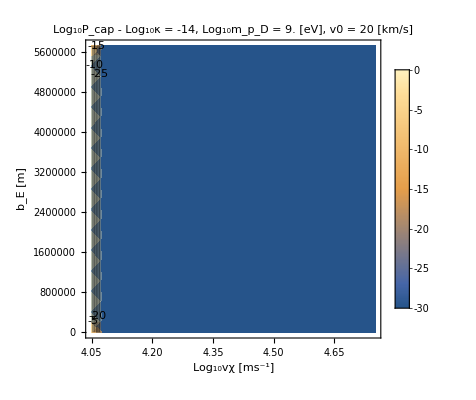

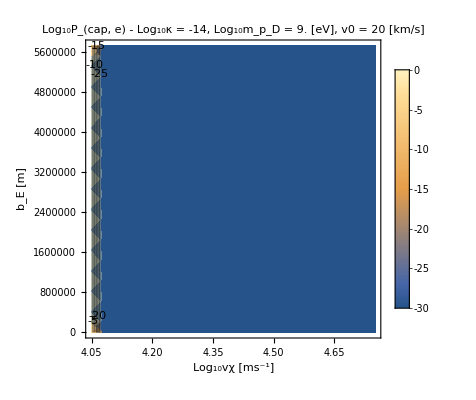

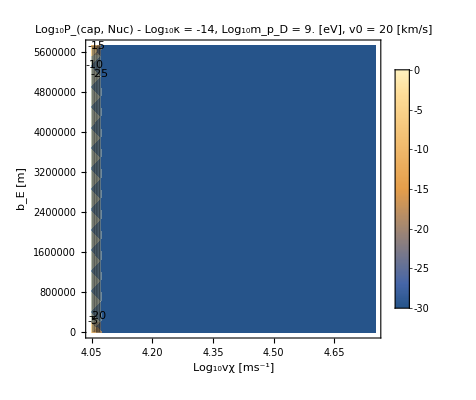

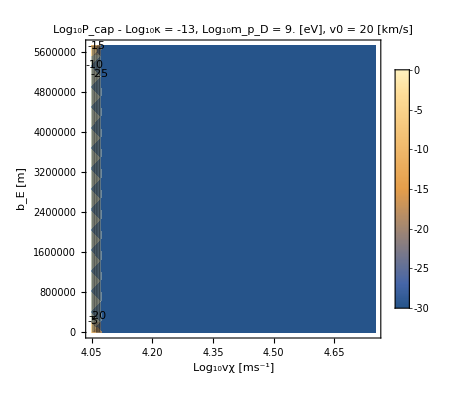

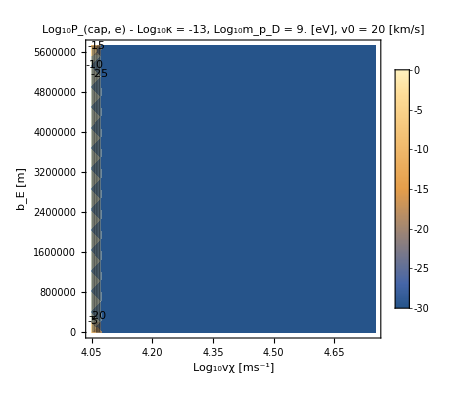

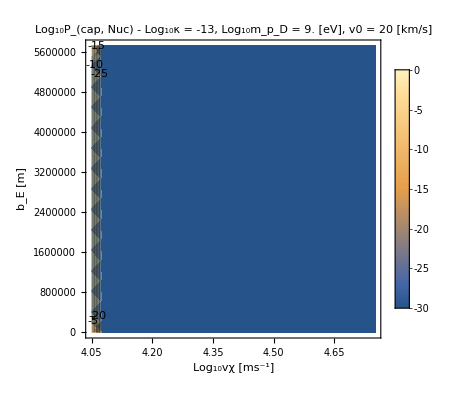

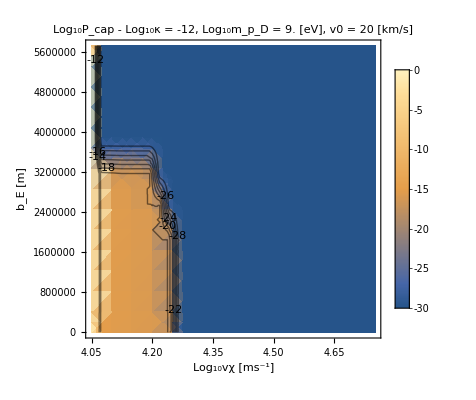

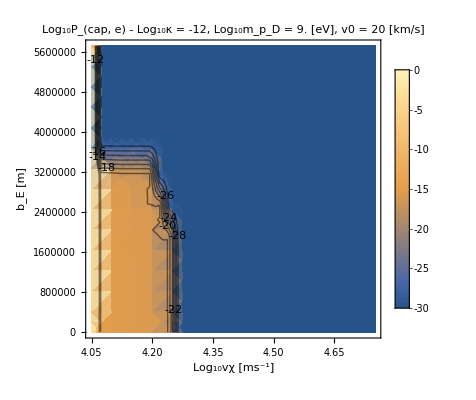

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {11852.68174912479798877029679715633392333984375}. NIntegrate obtained 1.04739×10^34 and 1.41715×10^31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19568.2}. NIntegrate obtained 7.53436×10^35 and 1.62816×10^31 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^16

1.×10^9

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21876.735141836}. NIntegrate obtained 3.01726×10^36 and 1.75059×10^33 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^18

1.×10^9

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^16

1.×10^9

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→2.96325×10^27 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→2.96325×10^25 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.04911×10^15 nD,NcMax→9.8501×10^32 nD,timeenoughforequil→True,Nc→3.64739×10^23 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.08331×10^16 nD,NcMax→1.26926×10^34 nD,timeenoughforequil→True,Nc→4.69994×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.53404×10^18 nD,NcMax→9.13037×10^35 nD,timeenoughforequil→True,Nc→3.38088×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→4.02395×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→4.02395×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→59528.1,βD→8.42612×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→4.02395×10^16 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→5.38095×10^24 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→5.38095×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.27666×10^13 nD,NcMax→1.78395×10^30 nD,timeenoughforequil→True,Nc→6.60578×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.34812×10^13 nD,NcMax→1.8838×10^30 nD,timeenoughforequil→True,Nc→6.9755×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.96594×10^16 nD,NcMax→2.74711×10^33 nD,timeenoughforequil→True,Nc→1.01723×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.10045×10^18 nD,NcMax→2.93507×10^35 nD,timeenoughforequil→True,Nc→1.08682×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.8794×10^19 nD,NcMax→5.4209×10^36 nD,timeenoughforequil→True,Nc→2.0073×10^19 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-31,vχMax→619683.,βD→6.96374×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44222×10^19 nD,NcMax→6.20736×10^36 nD,timeenoughforequil→True,Nc→2.29852×10^17 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→2.92755×10^27 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→2.92755×10^25 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.96423×10^15 nD,NcMax→9.73149×10^32 nD,timeenoughforequil→True,Nc→3.60347×10^23 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.98255×10^16 nD,NcMax→1.25518×10^34 nD,timeenoughforequil→True,Nc→4.6478×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.51963×10^18 nD,NcMax→9.11024×10^35 nD,timeenoughforequil→True,Nc→3.37342×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→4.0246×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→4.0246×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→59791.1,βD→8.34353×10^18,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→4.0246×10^16 nD,Γtotal→1.93265×10^16|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→5.30858×10^24 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→5.30858×10^22 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.2595×10^13 nD,NcMax→1.75996×10^30 nD,timeenoughforequil→True,Nc→6.51696×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.32998×10^13 nD,NcMax→1.85846×10^30 nD,timeenoughforequil→True,Nc→6.88167×10^18 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.94443×10^16 nD,NcMax→2.71705×10^33 nD,timeenoughforequil→True,Nc→1.0061×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.08999×10^18 nD,NcMax→2.92046×10^35 nD,timeenoughforequil→True,Nc→1.08141×10^20 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.8947×10^19 nD,NcMax→5.44228×10^36 nD,timeenoughforequil→True,Nc→2.01522×10^19 nD,Γtotal→1.93265×10^16|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-27,meD→1.78×10^-29,vχMax→622740.,βD→6.89548×10^16,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46382×10^19 nD,NcMax→6.23754×10^36 nD,timeenoughforequil→True,Nc→2.30969×10^17 nD,Γtotal→1.93265×10^16|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1GeVScan.dat

```mathematica
PDicts1GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[2]],NuclearσDicstallmasses[[2]]]
SaveIt[NotebookDirectory[]<>"PDicts1GeVScan",PDicts1GeVScan]
```

```mathematica
PDicts10GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicstallmasses[[3]],NuclearσDicstallmasses[[3]]]
SaveIt[NotebookDirectory[]<>"PDicts10GeVScan",PDicts10GeVScan]
Clear[PDicts10GeVScan]
```

mpD: 1.×10^10

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^17

InterpolatingFunction::dmval: Input value {-25.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 552.648, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 642.207, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^10

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {14811.1}. NIntegrate obtained 2.78284×10^35 and 1.04943×10^32 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^15

1.×10^10

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {318113.}. NIntegrate obtained 2.44235×10^23 and 2.56309×10^18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {318113.}. NIntegrate obtained 2.62377×10^25 and 2.41453×10^20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^17

1.×10^10

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^15

1.×10^10

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→7.52608×10^31 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→7.52608×10^29 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→7.52608×10^27 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→7.52608×10^25 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.41337×10^18 nD,NcMax→3.37233×10^35 nD,timeenoughforequil→True,Nc→3.17155×10^26 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77664×10^18 nD,NcMax→1.08667×10^36 nD,timeenoughforequil→True,Nc→1.02197×10^25 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→1.022×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→59528.1,βD→8.42612×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→1.022×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1591.35 nD,NcMax→2.22368×10^20 nD,timeenoughforequil→True,Nc→2.09129×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→170956. nD,NcMax→2.38886×10^22 nD,timeenoughforequil→True,Nc→2.24663×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.71628×10^7 nD,NcMax→2.39825×10^24 nD,timeenoughforequil→True,Nc→2.25546×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.72877×10^9 nD,NcMax→2.4157×10^26 nD,timeenoughforequil→True,Nc→2.27187×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.33694×10^15 nD,NcMax→3.26553×10^32 nD,timeenoughforequil→True,Nc→3.07111×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.00616×10^17 nD,NcMax→4.20067×10^34 nD,timeenoughforequil→True,Nc→3.95058×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.65712×10^19 nD,NcMax→2.31558×10^36 nD,timeenoughforequil→True,Nc→2.17772×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-30,vχMax→619683.,βD→6.96374×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44204×10^19 nD,NcMax→6.20711×10^36 nD,timeenoughforequil→True,Nc→5.83755×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→7.43541×10^31 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→7.43541×10^29 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→7.43541×10^27 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→7.43541×10^25 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.39429×10^18 nD,NcMax→3.34567×10^35 nD,timeenoughforequil→True,Nc→3.14648×10^26 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.7779×10^18 nD,NcMax→1.08685×10^36 nD,timeenoughforequil→True,Nc→1.02214×10^25 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→1.02217×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→59791.1,βD→8.34353×10^17,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→1.02217×10^21 nD,Γtotal→7.60943×10^11|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1657.76 nD,NcMax→2.31648×10^20 nD,timeenoughforequil→True,Nc→2.17857×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→179489. nD,NcMax→2.5081×10^22 nD,timeenoughforequil→True,Nc→2.35877×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.80108×10^7 nD,NcMax→2.51674×10^24 nD,timeenoughforequil→True,Nc→2.3669×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.81442×10^9 nD,NcMax→2.53539×10^26 nD,timeenoughforequil→True,Nc→2.38444×10^19 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.30762×10^15 nD,NcMax→3.22456×10^32 nD,timeenoughforequil→True,Nc→3.03257×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.9867×10^17 nD,NcMax→4.17347×10^34 nD,timeenoughforequil→True,Nc→3.92499×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.65846×10^19 nD,NcMax→2.31746×10^36 nD,timeenoughforequil→True,Nc→2.17949×10^23 nD,Γtotal→7.60943×10^11|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-26,meD→1.78×10^-28,vχMax→622740.,βD→6.89548×10^15,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46364×10^19 nD,NcMax→6.23728×10^36 nD,timeenoughforequil→True,Nc→5.86593×10^21 nD,Γtotal→7.60943×10^11|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10GeVScan.dat

#### Scan over the masses 10 MeV, 100 GeV, and 1 TeV - Post κ Bug Fix

switch to linear subdividing for impact parameter

```mathematica
PDicts1MeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1TeV[[1]],NuclearσDicst10MeVto1TeV[[1]]]
SaveIt[NotebookDirectory[]<>"PDicts1MeVScan",PDicts1MeVScan]
Clear[PDicts1MeVScan]
```

mpD: 1.×10^6

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^21

InterpolatingFunction::dmval: Input value {-29.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 467.32, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 478.105, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 494.243, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^6

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17542.}. NIntegrate obtained 8.93885×10^34 and 1.23357×10^31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {16573.}. NIntegrate obtained 8.60512×10^35 and 2.89145×10^31 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^19

1.×10^6

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {363736.}. NIntegrate obtained 3.15739×10^20 and 9.24472×10^15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^21

1.×10^6

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^19

1.×10^6

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.11712×10^15 nD,NcMax→1.56101×10^32 nD,timeenoughforequil→False,Nc→1.56101×10^32 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^32 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^30 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^28 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^26 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→1.10911×10^24 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.75206×10^17 nD,NcMax→1.08324×10^35 nD,timeenoughforequil→True,Nc→1.50131×10^24 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→59528.1,βD→8.42612×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.46263×10^18 nD,NcMax→1.04279×10^36 nD,timeenoughforequil→True,Nc→1.44526×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.05725 nD,NcMax→2.8747×10^17 nD,timeenoughforequil→False,Nc→2.8747×10^17 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→2.01403×10^29 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→2.01403×10^27 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45318×10^30 nD,timeenoughforequil→True,Nc→2.01404×10^25 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.04035×10^13 nD,NcMax→1.45374×10^30 nD,timeenoughforequil→True,Nc→2.01481×10^23 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.08043×10^13 nD,NcMax→1.50974×10^30 nD,timeenoughforequil→True,Nc→2.09242×10^21 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.93358×10^14 nD,NcMax→1.24834×10^32 nD,timeenoughforequil→True,Nc→1.73013×10^21 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-34,vχMax→619683.,βD→6.96374×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44222×10^19 nD,NcMax→6.20736×10^36 nD,timeenoughforequil→True,Nc→8.60309×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.10366×10^15 nD,NcMax→1.54221×10^32 nD,timeenoughforequil→False,Nc→1.54221×10^32 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^32 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^30 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^28 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^26 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→1.09575×10^24 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.70596×10^17 nD,NcMax→1.0768×10^35 nD,timeenoughforequil→True,Nc→1.49239×10^24 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→59791.1,βD→8.34353×10^21,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.46486×10^18 nD,NcMax→1.04311×10^36 nD,timeenoughforequil→True,Nc→1.44569×10^23 nD,Γtotal→5.16352×10^9|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.82067 nD,NcMax→3.94148×10^17 nD,timeenoughforequil→False,Nc→3.94148×10^17 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→1.98694×10^29 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→1.98694×10^27 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02597×10^13 nD,NcMax→1.43364×10^30 nD,timeenoughforequil→True,Nc→1.98695×10^25 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02638×10^13 nD,NcMax→1.43421×10^30 nD,timeenoughforequil→True,Nc→1.98775×10^23 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.06742×10^13 nD,NcMax→1.49156×10^30 nD,timeenoughforequil→True,Nc→2.06723×10^21 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→8.55446×10^14 nD,NcMax→1.19536×10^32 nD,timeenoughforequil→True,Nc→1.65671×10^21 nD,Γtotal→5.16352×10^9|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-30,meD→1.78×10^-32,vχMax→622740.,βD→6.89548×10^19,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46382×10^19 nD,NcMax→6.23754×10^36 nD,timeenoughforequil→True,Nc→8.64491×10^23 nD,Γtotal→5.16352×10^9|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1MeVScan.dat

```mathematica
PDicts10MeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1TeV[[2]],NuclearσDicst10MeVto1TeV[[2]]]
SaveIt[NotebookDirectory[]<>"PDicts10MeVScan",PDicts10MeVScan]
Clear[PDicts10MeVScan]
```

mpD: 1.×10^7

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^20

InterpolatingFunction::dmval: Input value {-28.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.×10^7

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21858.6}. NIntegrate obtained 8.56078×10^35 and 1.03503×10^31 for the integral and error estimates.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^18

1.×10^7

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {33625.1}. NIntegrate obtained 3.9926×10^37 and 2.99376×10^34 for the integral and error estimates.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^20

1.×10^7

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {21915.4}. NIntegrate obtained 8.68405×10^35 and 1.472×10^31 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^18

1.×10^7

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^29 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^27 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^25 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→True,Nc→8.9349×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.42419×10^18 nD,NcMax→1.03742×10^36 nD,timeenoughforequil→True,Nc→1.15829×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→1.21331×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→59528.1,βD→8.42612×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→True,Nc→1.21331×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→1.62248×10^27 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→True,Nc→1.62248×10^25 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45318×10^30 nD,timeenoughforequil→True,Nc→1.62249×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.04046×10^13 nD,NcMax→1.45389×10^30 nD,timeenoughforequil→True,Nc→1.62328×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.09103×10^13 nD,NcMax→1.52456×10^30 nD,timeenoughforequil→True,Nc→1.70218×10^19 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.60144×10^17 nD,NcMax→3.63513×10^34 nD,timeenoughforequil→True,Nc→4.05865×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.4391×10^19 nD,NcMax→6.20299×10^36 nD,timeenoughforequil→True,Nc→6.92569×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-33,vχMax→619683.,βD→6.96374×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.44222×10^19 nD,NcMax→6.20736×10^36 nD,timeenoughforequil→True,Nc→6.93057×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^29 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^27 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^25 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→True,Nc→8.82725×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.42063×10^18 nD,NcMax→1.03692×10^36 nD,timeenoughforequil→True,Nc→1.15774×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→1.21351×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→59791.1,βD→8.34353×10^20,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→True,Nc→1.21351×10^19 nD,Γtotal→6.40961×10^13|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→1.60066×10^27 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→True,Nc→1.60066×10^25 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02597×10^13 nD,NcMax→1.43364×10^30 nD,timeenoughforequil→True,Nc→1.60067×10^23 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02648×10^13 nD,NcMax→1.43435×10^30 nD,timeenoughforequil→True,Nc→1.60147×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.07756×10^13 nD,NcMax→1.50573×10^30 nD,timeenoughforequil→True,Nc→1.68116×10^19 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.58139×10^17 nD,NcMax→3.60712×10^34 nD,timeenoughforequil→True,Nc→4.02738×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46063×10^19 nD,NcMax→6.23308×10^36 nD,timeenoughforequil→True,Nc→6.95929×10^21 nD,Γtotal→6.40961×10^13|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-29,meD→1.78×10^-31,vχMax→622740.,βD→6.89548×10^18,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46382×10^19 nD,NcMax→6.23754×10^36 nD,timeenoughforequil→True,Nc→6.96426×10^19 nD,Γtotal→6.40961×10^13|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10MeVScan.dat

```mathematica
PDicts100GeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1TeV[[-2]],NuclearσDicst10MeVto1TeV[[-2]]]
SaveIt[NotebookDirectory[]<>"PDicts100GeVScan",PDicts100GeVScan]
Clear[PDicts100GeVScan]
```

mpD: 1.×10^11

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^16

InterpolatingFunction::dmval: Input value {-24.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 227.038, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 263.158, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 305.122, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^11

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {11853.1740880435}. NIntegrate obtained 2.24234×10^34 and 2.25617×10^31 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {24501.4}. NIntegrate obtained 8.35956×10^35 and 4.09971×10^30 for the integral and error estimates.

General::munfl: Exp[-1682.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1682.82] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1683.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^14

1.×10^11

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {318113.}. NIntegrate obtained 1.06876×10^32 and 8.22163×10^26 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^16

1.×10^11

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^14

1.×10^11

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.94463×10^17 nD,NcMax→2.71734×10^34 nD,timeenoughforequil→False,Nc→2.71734×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.24968×10^18 nD,NcMax→1.01304×10^36 nD,timeenoughforequil→False,Nc→1.01304×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→False,Nc→1.0867×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→59528.1,βD→8.42612×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→False,Nc→1.0867×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.96367×10^11 nD,NcMax→9.73071×10^28 nD,timeenoughforequil→False,Nc→9.73071×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.9632×10^13 nD,NcMax→9.73006×10^30 nD,timeenoughforequil→False,Nc→9.73006×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.91681×10^15 nD,NcMax→9.66524×10^32 nD,timeenoughforequil→False,Nc→9.66524×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.1106×10^17 nD,NcMax→5.74397×10^34 nD,timeenoughforequil→False,Nc→5.74397×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.51189×10^18 nD,NcMax→2.11264×10^35 nD,timeenoughforequil→False,Nc→2.11264×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.91243×10^18 nD,NcMax→4.0697×10^35 nD,timeenoughforequil→False,Nc→4.0697×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.03648×10^18 nD,NcMax→1.26272×10^36 nD,timeenoughforequil→False,Nc→1.26272×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-29,vχMax→619683.,βD→6.96374×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.4422×10^19 nD,NcMax→6.20733×10^36 nD,timeenoughforequil→False,Nc→6.20733×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.92417×10^17 nD,NcMax→2.68874×10^34 nD,timeenoughforequil→False,Nc→2.68874×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.2422×10^18 nD,NcMax→1.01199×10^36 nD,timeenoughforequil→False,Nc→1.01199×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→False,Nc→1.08688×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→59791.1,βD→8.34353×10^16,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→False,Nc→1.08688×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.24009×10^11 nD,NcMax→1.0117×10^29 nD,timeenoughforequil→False,Nc→1.0117×10^29 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.23962×10^13 nD,NcMax→1.01163×10^31 nD,timeenoughforequil→False,Nc→1.01163×10^31 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.19336×10^15 nD,NcMax→1.00517×10^33 nD,timeenoughforequil→False,Nc→1.00517×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.33145×10^17 nD,NcMax→6.05257×10^34 nD,timeenoughforequil→False,Nc→6.05257×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.60683×10^18 nD,NcMax→2.24531×10^35 nD,timeenoughforequil→False,Nc→2.24531×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.99909×10^18 nD,NcMax→4.19079×10^35 nD,timeenoughforequil→False,Nc→4.19079×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.228×10^18 nD,NcMax→1.28948×10^36 nD,timeenoughforequil→False,Nc→1.28948×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-25,meD→1.78×10^-27,vχMax→622740.,βD→6.89548×10^14,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.46379×10^19 nD,NcMax→6.2375×10^36 nD,timeenoughforequil→False,Nc→6.2375×10^36 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts100GeVScan.dat

```mathematica
PDicts1TeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1TeV[[-1]],NuclearσDicst10MeVto1TeV[[-1]]]
SaveIt[NotebookDirectory[]<>"PDicts1TeVScan",PDicts1TeVScan]
Clear[PDicts1TeVScan]
```

mpD: 1.×10^12

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^15

InterpolatingFunction::dmval: Input value {-23.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 551.562, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 635.678, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^12

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {14811.1}. NIntegrate obtained 3.36988×10^35 and 9.95499×10^31 for the integral and error estimates.

General::munfl: Exp[-25362.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-25366.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-25371.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^13

1.×10^12

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {14874.1790264059}. NIntegrate obtained 4.51491×10^35 and 2.79359×10^32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {43318.9}. NIntegrate obtained 5.86707×10^37 and 5.62905×10^34 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^15

1.×10^12

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^13

1.×10^12

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.92247×10^18 nD,NcMax→4.08372×10^35 nD,timeenoughforequil→False,Nc→4.08372×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77669×10^18 nD,NcMax→1.08668×10^36 nD,timeenoughforequil→False,Nc→1.08668×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→59528.1,βD→8.42612×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→False,Nc→1.0867×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→64.4479 nD,NcMax→9.00565×10^18 nD,timeenoughforequil→False,Nc→9.00565×10^18 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→22463.1 nD,NcMax→3.13889×10^21 nD,timeenoughforequil→False,Nc→3.13889×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.2431×10^6 nD,NcMax→3.13441×10^23 nD,timeenoughforequil→False,Nc→3.13441×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.2418×10^8 nD,NcMax→3.13258×10^25 nD,timeenoughforequil→False,Nc→3.13258×10^25 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.20924×10^10 nD,NcMax→3.08709×10^27 nD,timeenoughforequil→False,Nc→3.08709×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.94176×10^15 nD,NcMax→4.11067×10^32 nD,timeenoughforequil→False,Nc→4.11067×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.82278×10^17 nD,NcMax→5.34177×10^34 nD,timeenoughforequil→False,Nc→5.34177×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-28,vχMax→619683.,βD→6.96374×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.04209×10^19 nD,NcMax→2.85352×10^36 nD,timeenoughforequil→False,Nc→2.85352×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.8177×10^18 nD,NcMax→3.93733×10^35 nD,timeenoughforequil→False,Nc→3.93733×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77795×10^18 nD,NcMax→1.08685×10^36 nD,timeenoughforequil→False,Nc→1.08685×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→59791.1,βD→8.34353×10^15,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→False,Nc→1.08688×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→123.547 nD,NcMax→1.72639×10^19 nD,timeenoughforequil→False,Nc→1.72639×10^19 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→43207. nD,NcMax→6.03755×10^21 nD,timeenoughforequil→False,Nc→6.03755×10^21 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.31441×10^6 nD,NcMax→6.02875×10^23 nD,timeenoughforequil→False,Nc→6.02875×10^23 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.31139×10^8 nD,NcMax→6.02454×10^25 nD,timeenoughforequil→False,Nc→6.02454×10^25 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.1937×10^10 nD,NcMax→5.86008×10^27 nD,timeenoughforequil→False,Nc→5.86008×10^27 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.90691×10^15 nD,NcMax→4.06198×10^32 nD,timeenoughforequil→False,Nc→4.06198×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.64537×10^17 nD,NcMax→5.09388×10^34 nD,timeenoughforequil→False,Nc→5.09388×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-24,meD→1.78×10^-26,vχMax→622740.,βD→6.89548×10^13,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.93448×10^19 nD,NcMax→2.70316×10^36 nD,timeenoughforequil→False,Nc→2.70316×10^36 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1TeVScan.dat

#### Scan over the masses 10 TeV - 1 PeV Post κ Bug Fix

switch to linear subdividing for impact parameter

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^13 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^13 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts10TeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts10TeVScan",PDicts10TeVScan]
Clear[PDicts10TeVScan]
```

8

6

mpD: 1.×10^13

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^14

InterpolatingFunction::dmval: Input value {-22.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 1052.33, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1037.39, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 994.697, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^13

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {11852.6817491248}. NIntegrate obtained 6.17456×10^34 and 9.42643×10^31 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {27320.4}. NIntegrate obtained 8.49084×10^35 and 3.33652×10^30 for the integral and error estimates.

General::munfl: Exp[-14479.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14482.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14484.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^12

1.×10^13

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {278711.}. NIntegrate obtained 2.78537×10^23 and 3.56552×10^18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^14

1.×10^13

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^12

1.×10^13

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→59528.1,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→59528.1,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→59528.1,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→59528.1,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→59528.1,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.11939×10^16 nD,NcMax→1.56419×10^33 nD,timeenoughforequil→False,Nc→1.56419×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→59528.1,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.35478×10^17 nD,NcMax→7.48252×10^34 nD,timeenoughforequil→False,Nc→7.48252×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→59528.1,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.36353×10^18 nD,NcMax→1.02895×10^36 nD,timeenoughforequil→False,Nc→1.02895×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→59528.1,βD→8.42612×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→False,Nc→1.0867×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→619683.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1814.85 nD,NcMax→2.53599×10^20 nD,timeenoughforequil→False,Nc→2.53599×10^20 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→619683.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→238667. nD,NcMax→3.33503×10^22 nD,timeenoughforequil→False,Nc→3.33503×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→619683.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.40899×10^7 nD,NcMax→3.36621×10^24 nD,timeenoughforequil→False,Nc→3.36621×10^24 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→619683.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.40903×10^9 nD,NcMax→3.36627×10^26 nD,timeenoughforequil→False,Nc→3.36627×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→619683.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.40903×10^11 nD,NcMax→3.36627×10^28 nD,timeenoughforequil→False,Nc→3.36627×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→619683.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.50882×10^14 nD,NcMax→2.10836×10^31 nD,timeenoughforequil→False,Nc→2.10836×10^31 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→619683.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.92967×10^16 nD,NcMax→5.49114×10^33 nD,timeenoughforequil→False,Nc→5.49114×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-23,meD→1.78×10^-27,vχMax→619683.,βD→6.96374×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.72559×10^18 nD,NcMax→5.20596×10^35 nD,timeenoughforequil→False,Nc→5.20596×10^35 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→59791.1,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→59791.1,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→59791.1,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→59791.1,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→59791.1,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.10593×10^16 nD,NcMax→1.54537×10^33 nD,timeenoughforequil→False,Nc→1.54537×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→59791.1,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.29655×10^17 nD,NcMax→7.40115×10^34 nD,timeenoughforequil→False,Nc→7.40115×10^34 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→59791.1,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.35763×10^18 nD,NcMax→1.02812×10^36 nD,timeenoughforequil→False,Nc→1.02812×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→59791.1,βD→8.34353×10^14,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77813×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→False,Nc→1.08688×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→622740.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1788.17 nD,NcMax→2.4987×10^20 nD,timeenoughforequil→False,Nc→2.4987×10^20 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→622740.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→245703. nD,NcMax→3.43334×10^22 nD,timeenoughforequil→False,Nc→3.43334×10^22 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→622740.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.48125×10^7 nD,NcMax→3.46719×10^24 nD,timeenoughforequil→False,Nc→3.46719×10^24 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→622740.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.48141×10^9 nD,NcMax→3.46741×10^26 nD,timeenoughforequil→False,Nc→3.46741×10^26 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→622740.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.48141×10^11 nD,NcMax→3.46741×10^28 nD,timeenoughforequil→False,Nc→3.46741×10^28 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→622740.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.49853×10^14 nD,NcMax→2.09398×10^31 nD,timeenoughforequil→False,Nc→2.09398×10^31 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→622740.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.90078×10^16 nD,NcMax→5.45077×10^33 nD,timeenoughforequil→False,Nc→5.45077×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-23,meD→1.78×10^-25,vχMax→622740.,βD→6.89548×10^12,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.72274×10^18 nD,NcMax→5.20199×10^35 nD,timeenoughforequil→False,Nc→5.20199×10^35 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts10TeVScan.dat

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^14 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^14 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts100TeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts100TeVScan",PDicts100TeVScan]
Clear[PDicts100TeVScan]
```

9

7

mpD: 1.×10^14

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^13

InterpolatingFunction::dmval: Input value {-21.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 776.663, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 776.664, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 123.044, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^14

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {13329.6825168354}. NIntegrate obtained 1.45689×10^35 and 1.46274×10^32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {15692.1}. NIntegrate obtained 3.62417×10^35 and 2.74488×10^31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19568.2}. NIntegrate obtained 6.37142×10^35 and 3.31707×10^31 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-147473.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-147500.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-147526.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^11

1.×10^14

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^13

1.×10^14

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^11

1.×10^14

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→59528.1,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→59528.1,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→59528.1,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.72692×10^15 nD,NcMax→8.00253×10^32 nD,timeenoughforequil→False,Nc→8.00253×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→59528.1,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.26346×10^18 nD,NcMax→1.76551×10^35 nD,timeenoughforequil→False,Nc→1.76551×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→59528.1,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.143×10^18 nD,NcMax→4.39188×10^35 nD,timeenoughforequil→False,Nc→4.39188×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→59528.1,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.5255×10^18 nD,NcMax→7.72107×10^35 nD,timeenoughforequil→False,Nc→7.72107×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→59528.1,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.3136×10^18 nD,NcMax→1.02197×10^36 nD,timeenoughforequil→False,Nc→1.02197×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→59528.1,βD→8.42612×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77686×10^18 nD,NcMax→1.0867×10^36 nD,timeenoughforequil→False,Nc→1.0867×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→619683.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→False,Nc→1.45317×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→619683.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.03995×10^13 nD,NcMax→1.45317×10^30 nD,timeenoughforequil→False,Nc→1.45317×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→619683.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.16375×10^13 nD,NcMax→1.62617×10^30 nD,timeenoughforequil→False,Nc→1.62617×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→619683.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.62221×10^14 nD,NcMax→1.34456×10^32 nD,timeenoughforequil→False,Nc→1.34456×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→619683.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.59713×10^15 nD,NcMax→3.62911×10^32 nD,timeenoughforequil→False,Nc→3.62911×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→619683.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.99824×10^15 nD,NcMax→1.39711×10^33 nD,timeenoughforequil→False,Nc→1.39711×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→619683.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.13395×10^16 nD,NcMax→4.37924×10^33 nD,timeenoughforequil→False,Nc→4.37924×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-22,meD→1.78×10^-26,vχMax→619683.,βD→6.96374×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.87767×10^17 nD,NcMax→8.21319×10^34 nD,timeenoughforequil→False,Nc→8.21319×10^34 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→59791.1,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→59791.1,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→59791.1,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.65792×10^15 nD,NcMax→7.90612×10^32 nD,timeenoughforequil→False,Nc→7.90612×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→59791.1,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.25078×10^18 nD,NcMax→1.74779×10^35 nD,timeenoughforequil→False,Nc→1.74779×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→59791.1,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.1199×10^18 nD,NcMax→4.35961×10^35 nD,timeenoughforequil→False,Nc→4.35961×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→59791.1,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.50326×10^18 nD,NcMax→7.69001×10^35 nD,timeenoughforequil→False,Nc→7.69001×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→59791.1,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.30654×10^18 nD,NcMax→1.02098×10^36 nD,timeenoughforequil→False,Nc→1.02098×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→59791.1,βD→8.34353×10^13,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77812×10^18 nD,NcMax→1.08688×10^36 nD,timeenoughforequil→False,Nc→1.08688×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→622740.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→False,Nc→1.43363×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→622740.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.02596×10^13 nD,NcMax→1.43363×10^30 nD,timeenoughforequil→False,Nc→1.43363×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→622740.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.1481×10^13 nD,NcMax→1.60431×10^30 nD,timeenoughforequil→False,Nc→1.60431×10^30 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→622740.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.53215×10^14 nD,NcMax→1.33198×10^32 nD,timeenoughforequil→False,Nc→1.33198×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→622740.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.57464×10^15 nD,NcMax→3.59768×10^32 nD,timeenoughforequil→False,Nc→3.59768×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→622740.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.92543×10^15 nD,NcMax→1.38693×10^33 nD,timeenoughforequil→False,Nc→1.38693×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→622740.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.10233×10^16 nD,NcMax→4.33506×10^33 nD,timeenoughforequil→False,Nc→4.33506×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-22,meD→1.78×10^-24,vχMax→622740.,βD→6.89548×10^11,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.8491×10^17 nD,NcMax→8.17326×10^34 nD,timeenoughforequil→False,Nc→8.17326×10^34 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts100TeVScan.dat

```mathematica
eind = FirstPosition["mχ"/.ElectronicσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
Nucind = FirstPosition["mχ"/.NuclearσDicst10MeVto1PeV,10^15 ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]
PDicts1PeVScan=ScanGetCaptureRateandGetNc[meDPoints,κpoints,v0Points,ElectronicσDicst10MeVto1PeV[[eind]],NuclearσDicst10MeVto1PeV[[Nucind]]]
SaveIt[NotebookDirectory[]<>"PDicts1PeVScan",PDicts1PeVScan]
Clear[PDicts1PeVScan]
```

10

8

mpD: 1.×10^15

meD/mpD: 1/10000

v0: 20000

βD: 8.42612×10^12

InterpolatingFunction::dmval: Input value {-20.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 27.6026, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^15

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {15692.1}. NIntegrate obtained 3.62115×10^35 and 3.67111×10^31 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {17542.}. NIntegrate obtained 5.04223×10^35 and 1.6774×10^32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in vχ near {vχ} = {19568.2}. NIntegrate obtained 6.36921×10^35 and 2.4728×10^31 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-1.47764×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.4779×10^6] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::munfl: Exp[-2.78713×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

meD/mpD: 1/10000

v0: 220000

βD: 6.96374×10^10

1.×10^15

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

meD/mpD: 1/100

v0: 20000

βD: 8.34353×10^12

1.×10^15

20000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

meD/mpD: 1/100

v0: 220000

βD: 6.89548×10^10

1.×10^15

220000

-Graphics-

-Graphics-

-Graphics-

«21 more identical outputs»

{{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.14038×10^18 nD,NcMax→4.38822×10^35 nD,timeenoughforequil→False,Nc→4.38822×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.37278×10^18 nD,NcMax→6.11033×10^35 nD,timeenoughforequil→False,Nc→6.11033×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.52358×10^18 nD,NcMax→7.7184×10^35 nD,timeenoughforequil→False,Nc→7.7184×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.47201×10^18 nD,NcMax→9.04369×10^35 nD,timeenoughforequil→False,Nc→9.04369×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.84734×10^18 nD,NcMax→9.56816×10^35 nD,timeenoughforequil→False,Nc→9.56816×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.37205×10^18 nD,NcMax→1.03014×10^36 nD,timeenoughforequil→False,Nc→1.03014×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.70231×10^18 nD,NcMax→1.07629×10^36 nD,timeenoughforequil→False,Nc→1.07629×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→59528.1,βD→8.42612×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77201×10^18 nD,NcMax→1.08603×10^36 nD,timeenoughforequil→False,Nc→1.08603×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.59105×10^15 nD,NcMax→3.62061×10^32 nD,timeenoughforequil→False,Nc→3.62061×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.1916×10^15 nD,NcMax→7.2545×10^32 nD,timeenoughforequil→False,Nc→7.2545×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.98007×10^15 nD,NcMax→1.39457×10^33 nD,timeenoughforequil→False,Nc→1.39457×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.70493×10^16 nD,NcMax→2.38239×10^33 nD,timeenoughforequil→False,Nc→2.38239×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.82901×10^16 nD,NcMax→2.55578×10^33 nD,timeenoughforequil→False,Nc→2.55578×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.16162×10^16 nD,NcMax→4.4179×10^33 nD,timeenoughforequil→False,Nc→4.4179×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.37614×10^16 nD,NcMax→7.51237×10^33 nD,timeenoughforequil→False,Nc→7.51237×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-25,vχMax→619683.,βD→6.96374×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.40792×10^17 nD,NcMax→1.96736×10^34 nD,timeenoughforequil→False,Nc→1.96736×10^34 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.11732×10^18 nD,NcMax→4.356×10^35 nD,timeenoughforequil→False,Nc→4.356×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→4.34759×10^18 nD,NcMax→6.07512×10^35 nD,timeenoughforequil→False,Nc→6.07512×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.50134×10^18 nD,NcMax→7.68732×10^35 nD,timeenoughforequil→False,Nc→7.68732×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.45564×10^18 nD,NcMax→9.02082×10^35 nD,timeenoughforequil→False,Nc→9.02082×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→6.83453×10^18 nD,NcMax→9.55025×10^35 nD,timeenoughforequil→False,Nc→9.55025×10^35 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.36096×10^18 nD,NcMax→1.02859×10^36 nD,timeenoughforequil→False,Nc→1.02859×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.70178×10^18 nD,NcMax→1.07621×10^36 nD,timeenoughforequil→False,Nc→1.07621×10^36 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→59791.1,βD→8.34353×10^12,v0→20000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→7.77313×10^18 nD,NcMax→1.08618×10^36 nD,timeenoughforequil→False,Nc→1.08618×10^36 nD,Γtotal→0.|>},{<|Pf→InterpolatingFunction[…],κ→1/100000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→2.56956×10^15 nD,NcMax→3.59059×10^32 nD,timeenoughforequil→False,Nc→3.59059×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.14688×10^15 nD,NcMax→7.19202×10^32 nD,timeenoughforequil→False,Nc→7.19202×10^32 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→9.91201×10^15 nD,NcMax→1.38506×10^33 nD,timeenoughforequil→False,Nc→1.38506×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.74471×10^16 nD,NcMax→2.43798×10^33 nD,timeenoughforequil→False,Nc→2.43798×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.72046×10^16 nD,NcMax→2.4041×10^33 nD,timeenoughforequil→False,Nc→2.4041×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/1000000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→3.12719×10^16 nD,NcMax→4.3698×10^33 nD,timeenoughforequil→False,Nc→4.3698×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/100000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→5.30808×10^16 nD,NcMax→7.41727×10^33 nD,timeenoughforequil→False,Nc→7.41727×10^33 nD,Γtotal→0.|>,<|Pf→InterpolatingFunction[…],κ→1/10000000,mpD→1.78×10^-21,meD→1.78×10^-23,vχMax→622740.,βD→6.89548×10^10,v0→220000,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],dNcMaxdt→1.39987×10^17 nD,NcMax→1.95611×10^34 nD,timeenoughforequil→False,Nc→1.95611×10^34 nD,Γtotal→0.|>}}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDicts1PeVScan.dat

#### Get KE change

```mathematica
"mpD"("c")^2/("JpereV")/.PDicts1MeVScan/.SIConstRepl
```

{{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}}

```mathematica
"mpD"("c")^2/("JpereV")/.PDicts1MeVKE/.SIConstRepl
```

{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}

```mathematica
PlotKEchangeκContour[{PDicts1MeVKE,PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[{PDicts10MeVKE,PDictsp1GeVKE,PDicts1GeVKE,PDicts10GeVKE,PDicts100GeVKE,PDicts1TeVKE,PDicts10TeVKE,PDicts100TeVKE,PDicts1PeVKE}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"Γtotal"/.PDicts10GeVKE
```

{7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11,7.60943×10^11}

#### Get Plots for Pcap E and Nuc

```mathematica
"mχ"("c")^2/("JpereV")/.ElectronicσDicst10MeVto1TeV[[3]]/.Constants`SIConstRepl
```

{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8}

```mathematica
PDict1MeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[1]],NuclearσDicst10MeVto1TeV[[1]]]
PlotPDist[PDict1MeV]
```

InterpolatingFunction::dmval: Input value {-29.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 471.036, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 467.725, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 511.325, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^6

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PDictp1GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[3]],NuclearσDicst10MeVto1TeV[[3]]]
PlotPDist[PDictp1GeV]
```

InterpolatingFunction::dmval: Input value {-27.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 640.912, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 762.958, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^8

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PDict1GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[4]],NuclearσDicst10MeVto1TeV[[4]]]
PlotPDist[PDict1GeV]
```

InterpolatingFunction::dmval: Input value {-26.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 340.432, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 491.321, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

1.×10^9

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PDict100GeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[6]],NuclearσDicst10MeVto1TeV[[6]]]
PlotPDist[PDict100GeV]
```

InterpolatingFunction::dmval: Input value {-24.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 305.666, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 436.713, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

General::munfl: Exp[-3360.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3360.63] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.×10^11

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PDict1TeV=IterateGetCaptureRate[("meD/mpD"/.meDPoints[[1]]),κpoints, v0Points[[2]],ElectronicσDicst10MeVto1TeV[[7]],NuclearσDicst10MeVto1TeV[[7]]]
PlotPDist[PDict1TeV]
```

InterpolatingFunction::dmval: Input value {-23.7496,4.04922} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 551.562, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 776.104, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

General::munfl: Exp[-26086.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26137.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.×10^12

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

#### Soft Scatter Regime

```mathematica
PlotELNucoverE[PDict1MeV]
```

1.×10^6

220000

InterpolatingFunction::dmval: Input value {-29.7496,4.04934} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
PlotELNucoverE[PDict1GeV]
```

1.×10^9

220000

InterpolatingFunction::dmval: Input value {-26.7496,4.04934} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
PlotELNucoverE[PDict1TeV]
```

1.×10^12

220000

InterpolatingFunction::dmval: Input value {-23.7496,4.04934} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

#### Hard Scatter Regime

```mathematica
PlotPDist[PDict1MeV]
```

1.×10^6

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PlotPDist[PDict1GeV]
```

1.×10^9

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

```mathematica
PlotPDist[PDict1TeV]
```

1.×10^12

220000

-Graphics-

-Graphics-

-Graphics-

«12 more identical outputs»

## Scrap